# Normal Distribution Function

### Init

```mathematica
ValueThumbSlider[v_]:=ValueThumbSlider[v,{0,1}];
ValueThumbSlider[Dynamic[var_],{min_,max_},options___]:=LocatorPane[Dynamic[If[!NumberQ[var],var=min];{var,0},(var=First[#])&],
Graphics[{AbsoluteThickness[1.5],Line[{{min,0},{max,0}}],
Dynamic[{Text[var,{var,0},{0,-1}],Polygon[{Offset[{0,-1},{var,0}],Offset[{-5,-8},{var,0}],Offset[{5,-8},{var,0}]}]}]},
ImageSize->{300,30},PlotRange->{{min,max}+0.1{-1,1}(max-min),{-1,1}},AspectRatio->1/10],
{{min,0},{max,0}},Appearance->None];
ValueThumbSlider[Dynamic[var_],{min_,max_,scale_},options___]:=LocatorPane[Dynamic[If[!NumberQ[var],var=min];{var,0},(var=First[#])&],
Graphics[{AbsoluteThickness[1.5],Line[{{min,0},{max,0}}],
Dynamic[{Text[var,{var,0},{0,-1}],Polygon[{Offset[{0,-1},{var,0}],Offset[{-5,-8},{var,0}],Offset[{5,-8},{var,0}]}]}]},
ImageSize->{300,30},PlotRange->{{min,max}+0.1{-1,1}(max-min),{-1,1}},AspectRatio->1/10],
{{min,0},{max,0},{scale,0}},Appearance->None];
```

## Definition

```mathematica
FullSimplify[Integrate[PDF[NormalDistribution[0,1],t],{t,0,x}]]
```

1/2 Erf[x/(√2)]

## The relationship of the Normal Distribution to the error Function

```mathematica
Print["∫"," = ",FullSimplify[Integrate[ A PDF[NormalDistribution[μ,σ] ,t],{t,sMin,x}]]]
Print["∫"," = ",FullSimplify[Integrate[ A PDF[NormalDistribution[μ,σ] ,a t],{t,sMin,x}]]]
```

∫ = 1/2 A (-Erf[(sMin-μ)/(√2 σ)]+Erf[(x-μ)/(√2 σ)])

∫ = (A (Erf[(-a sMin+μ)/(√2 σ)]-Erf[(-a x+μ)/(√2 σ)]))/(2 a)

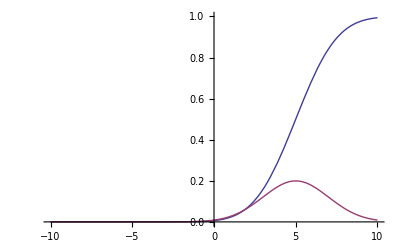

```mathematica
μ =5; σ =2; sMax = 10; sMin = -10; A=1;
Plot[{1/2 A (-Erf[(sMin-μ)/(√2 σ)]+Erf[(x-μ)/(√2 σ)]),PDF[NormalDistribution[μ,σ],x]},{x,sMin,sMax},PlotRange->{Automatic,{0,1}}]
Clear[μ , σ ,sMax ,sMin ,A]
```

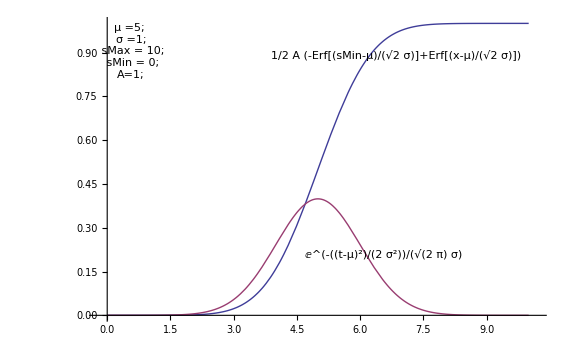

## First we make an adjustable version of the error function

The maximum taken on the Range sMin to sMax is

```mathematica
Print["∫"," = ",FullSimplify[Integrate[ A PDF[NormalDistribution[μ,σ] ,t],{t,sMin,sMax}]]]
```

∫ = 1/2 A (Erf[(sMax-μ)/(√2 σ)]-Erf[(sMin-μ)/(√2 σ)])

Scaling and shifting to the destination range.

```mathematica
dis[ x_,σ_,μ_,sMin_,sMax_,dMin_,dMax_]:=Evaluate[dMin + FullSimplify[(dMax - dMin) Integrate[ A PDF[NormalDistribution[μ,σ] ,t],{t,sMin,x}]]/FullSimplify[Integrate[ A PDF[NormalDistribution[μ,σ] ,t],{t,sMin,sMax}]]]
```

```mathematica
dis[ x,σ,μ,sMin,sMax,dMin,dMax]
```

dMin+((dMax-dMin) (-Erf[(sMin-μ)/(√2 σ)]+Erf[(x-μ)/(√2 σ)]))/(Erf[(sMax-μ)/(√2 σ)]-Erf[(sMin-μ)/(√2 σ)])

```mathematica
Manipulate[Plot[dis[ x,g,c,sMin,sMax,dMin,dMax],{x,0,255},Frame -> True,PlotRange -> {{sMin,sMax},{dMin,dMax}}],
{{dMin,0},-255,255,1,ValueThumbSlider[##]&},{{dMax,255},1,255,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{{c,(sMax+sMin)/2},sMin,sMax,1,ValueThumbSlider[##]&},{{g,40},1,100,ValueThumbSlider[##]&}
]
```

```mathematica
eErf[ x_,g_,c_,xMin_,xMax_,yMin_,yMax_]:=yMin+((-yMax+yMin)*(Erf[(g*(-c+x))/(xMax-xMin)]+Erf[(g*(c-xMin))/(xMax-xMin)]))/(Erf[(g*(c-xMax))/(xMax-xMin)]+Erf[(g*(-c+xMin))/(xMax-xMin)])
```

```mathematica
eErf[ x,g,c,sMin,sMax,dMin,dMax]
```

dMin+((-dMax+dMin) (Erf[(g (c-sMin))/(sMax-sMin)]+Erf[(g (-c+x))/(sMax-sMin)]))/(Erf[(g (c-sMax))/(sMax-sMin)]+Erf[(g (-c+sMin))/(sMax-sMin)])

Tidying up and making sure that the terms in the Erf are always positive and intriducing a rational version of the error function Erf[a, b] = Erf[a/b]

```mathematica
Unprotect[Erf];
Erf[a_,b_]:=Erf[a/b];
Protect[Erf];
```

```mathematica
aErf[x_, g_,c_,xMin_,xMax_,yMin_,yMax_,erf_:Function[{a,b},Erf[a,b]]]:=yMin+((yMax-yMin)*(Piecewise[{{erf[(g*(-c+x)),(xMax-xMin)],x≥c},{-erf[(g*(c-x)),(xMax-xMin)],x<c}}]+erf[(g*(c-xMin)),(xMax-xMin)]))/( erf[(g*(-c+xMax)),(xMax-xMin)]+erf[(g*(c-xMin)),(xMax-xMin)]);
```

```mathematica
aErf[x, g,c,xMin,xMax,yMin,yMax]
```

yMin+((yMax-yMin) (Erf[(g (c-xMin))/(xMax-xMin)]+(Piecewise[{{Erf[(g (-c+x))/(xMax-xMin)], x≥c}, {-Erf[(g (c-x))/(xMax-xMin)], x<c}, {0, True}}])))/(Erf[(g (-c+xMax))/(xMax-xMin)]+Erf[(g (c-xMin))/(xMax-xMin)])

We are interested in the maximum gradient at c

```mathematica
FullSimplify[D[eErf[ x,g,c,sMin,sMax,dMin,dMax],x]]/.x->c
```

(2 (-dMax+dMin) g)/(√π (sMax-sMin) (Erf[(g (c-sMax))/(sMax-sMin)]+Erf[(g (-c+sMin))/(sMax-sMin)]))

We are interested in where the gradient of the distribution function equals one in the src dst space however in the unit 0:1 space this is where the gradient is equal to dRange/sRange.

```mathematica
FullSimplify[D[eErf[ x,g,c,0,1,0,1],x]]==dRange/sRange
```

(2 ⅇ^(-g^2 (c-x)^2) g)/(√π (Erf[c g]+Erf[g-c g]))==dRange/sRange

```mathematica
Solve[(2*g)/(E^(g^2*(c - x)^2)*(Sqrt[Pi]*(Erf[(1 - c)*g] + Erf[c*g])))==dRange/sRange,x,InverseFunctions->True]
```

{{x→ConditionalExpression[(c g-√(2 ⅈ π C[1]+Log[(2 g sRange)/(dRange √π (Erf[(1-c) g]+Erf[c g]))]))/g,C[1]∈Integers]},{x→ConditionalExpression[(c g+√(2 ⅈ π C[1]+Log[(2 g sRange)/(dRange √π (Erf[(1-c) g]+Erf[c g]))]))/g,C[1]∈Integers]}}

```mathematica
D[(Erf[c*g] - Erf[g*(c - x)])/(Erf[c*g] + Erf[g*(1 - c)]),x] == dRange/sRange
```

(2 ⅇ^(-g^2 (c-x)^2) g)/(√π (Erf[(1-c) g]+Erf[c g]))==dRange/sRange

```mathematica
E^(g^2*(c - x)^2) == (2*g)/(dRange/sRange*(Sqrt[Pi]*(Erf[(1 - c)*g] + Erf[c*g])))
```

ⅇ^(g^2 (c-x)^2)==(2 g sRange)/(dRange √π (Erf[(1-c) g]+Erf[c g]))

```mathematica
(c - x)^2 == Log[(2*g)/(dRange/sRange*(Sqrt[Pi]*(Erf[(1 - c)*g] + Erf[c*g])))]/g^2
```

(c-x)^2==Log[(2 g sRange)/(dRange √π (Erf[(1-c) g]+Erf[c g]))]/g^2

```mathematica
x == c - Sqrt[Log[(2*g)/(dRange/sRange*(Sqrt[Pi]*(Erf[(1 - c)*g] + Erf[c*g])))]]/g
```

x==c-(√Log[(2 g sRange)/(dRange √π (Erf[(1-c) g]+Erf[c g]))])/g

```mathematica
unitGrad[ g_,c_,sMin_,sMax_,dMin_,dMax_]:={c + ((sMax - sMin)*Sqrt[Log[(2*(dMax - dMin)*g)/(Sqrt[Pi]*(sMax - sMin)*
        (Erf[(g*(-c + sMax))/(sMax - sMin)] + 
         Erf[(g*(c - sMin))/(sMax - sMin)]))]])/g, c - ((sMax - sMin)*Sqrt[Log[(2*(dMax - dMin)*g)/(Sqrt[Pi]*(sMax - sMin)*
        (Erf[(g*(-c + sMax))/(sMax - sMin)] + 
         Erf[(g*(c - sMin))/(sMax - sMin)]))]])/g }
```

```mathematica
unitGrad[ g,c,sMin,sMax,dMin,dMax]
```

{c+((sMax-sMin) √Log[(2 (dMax-dMin) g)/(√π (sMax-sMin) (Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)]))])/g,c-((sMax-sMin) √Log[(2 (dMax-dMin) g)/(√π (sMax-sMin) (Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)]))])/g}

and where the function equals dMin + 1 and dMax - 1 because here the function can be replaced with a simple range test.

For efficiency it is useful to have the values at which upon rounding the function is constant. This is where the function equals dL = {1/dRange, 1 - 1/dRange}.

```mathematica
FullSimplify[eErf[ x,g,c,0,1,0,1]]==dL
```

(Erf[c g]-Erf[g (c-x)])/(Erf[c g]+Erf[g-c g])==dL

```mathematica
Solve[(Erf[c g]-Erf[g (c-x)])/(Erf[c g]+Erf[g-c g])==dL ,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(c g-InverseErf[Erf[c g]-dL Erf[c g]-dL Erf[g-c g]])/g}}

```mathematica
x== FullSimplify[(c g-InverseErf[Erf[c g]-dL Erf[c g]-dL Erf[g-c g]])/g]
```

x==c-InverseErf[-(-1+dL) Erf[c g]-dL Erf[g-c g]]/g

```mathematica
x == c + InverseErf[( dL - 1)*Erf[c*g] + dL*Erf[g - c*g]]/g
```

x==c+InverseErf[(-1+dL) Erf[c g]+dL Erf[g-c g]]/g

```mathematica
uErfLowHigh[ dL_]:=c + InverseErf[( dL - 1)*Erf[c*g] + dL*Erf[g - c*g]]/g
uErfLowHigh =  FullSimplify[{uErfLowHigh[ 1/dRange], uErfLowHigh[ 1 - 1/dRange]}]
```

{c+InverseErf[(-(-1+dRange) Erf[c g]+Erf[g-c g])/dRange]/g,c+InverseErf[(-Erf[c g]+(-1+dRange) Erf[g-c g])/dRange]/g}

all that remains is to scale these values to the source range

```mathematica
FullSimplify[{sMin + sRange(c + InverseErf[((-(-1 + dRange))*Erf[c*g] + Erf[g - c*g])/dRange]/g), sMin + sRange(c + InverseErf[(-Erf[c*g] + (-1 + dRange)*Erf[g - c*g])/dRange]/g)}]
```

{sMin+c sRange+(sRange InverseErf[(-(-1+dRange) Erf[c g]+Erf[g-c g])/dRange])/g,sMin+c sRange+(sRange InverseErf[(-Erf[c g]+(-1+dRange) Erf[g-c g])/dRange])/g}

Recognising that c sRange + sMin is c in the source space we can simplify by letting c be in the range sMin..sMax and uC be in the range 0..1
Let : c = uC sRange + sMin
Let : lL = 1 / dRange
Let : uL = (dRange -1) / dRange

```mathematica
{c + (sRange*InverseErf[(-uL Erf[uC*g] + lL Erf[g(1 - uC)])])/g, 
  c - (sRange*InverseErf[(lL Erf[uC*g] - uL Erf[g ( 1 - uC)])])/g}
```

{c+(sRange InverseErf[lL Erf[g (1-uC)]-uL Erf[g uC]])/g,c-(sRange InverseErf[-uL Erf[g (1-uC)]+lL Erf[g uC]])/g}

```mathematica
eErfLowHigh[ x_,grad_,c_,sMin_,sMax_,dMin_,dMax_]:=Evaluate[{FullSimplify[Solve[eErf[ x,grad,c,sMin,sMax,dMin,dMax]==dMin + 1,x]][[1,1,2]],
FullSimplify[Solve[eErf[ x,grad,c,sMin,sMax,dMin,dMax]==dMax - 1,x]][[1,1,2]]}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
eErfLowHigh[ x,g,c,sMin,sMax,dMin,dMax]
```

{c+((sMax-sMin) InverseErf[(-Erf[(g (c-sMax))/(sMax-sMin)]+(1-dMax+dMin) Erf[(g (c-sMin))/(sMax-sMin)])/(dMax-dMin)])/g,c+((sMax-sMin) InverseErf[((1-dMax+dMin) Erf[(g (c-sMax))/(sMax-sMin)]-Erf[(g (c-sMin))/(sMax-sMin)])/(dMax-dMin)])/g}

```mathematica
sLowHigh = N[eErfLowHigh[ x,8,140,0,255,0,255]]
```

{80.0744,199.925}

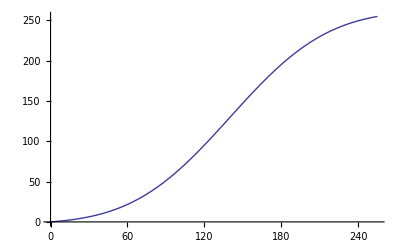

```mathematica
Plot[nErf[x],{x,0,255}]
```

```mathematica
Clear[dRange,sRange, ErfA,ErfB, grad,con,ErfA,ErfB,iErf,shift,scale,g]
```

```mathematica
{FullSimplify[Solve[shift +scale  Erf[((grad*(x-con))/sRange)]==dMin + 1,x]][[1,1,2]],
FullSimplify[Solve[shift +scale  Erf[((grad*(x-con))/sRange)]==dMax ,x]][[1,1,2]]}
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{con+(sRange InverseErf[1/255 ((1+dMin) Erf[23/17]+(-254+dMin) Erf[28/17])])/grad,con+(sRange InverseErf[1/255 (dMax Erf[23/17]+(-255+dMax) Erf[28/17])])/grad}

```mathematica
Clear[setUprErf];
Clear[dRange,sRange, g,grad,con,shift,scale,ErfA,ErfB,ErfAB,iErf,nErf,sUnitGrad,dUnitGrad,sLowHigh,shiftednErf,pErf];
setUprErf[ g_,c_,sMin_,sMax_,dMin_,dMax_]:=Module[{ σ,grad,con,dRange,sRange},
Clear[dRange,sRange, grad,con,shift,scale,ErfA,ErfB,ErfAB,iErf,nErf,sUnitGrad,dUnitGrad,sLowHigh,shiftednErf,pErf];
grad= g;
con = c;
dRange = dMax-dMin;
sRange = sMax-sMin;
ErfA = Erf[g (c-sMin)/sRange];
ErfB = Erf[g (-c+sMax)/sRange];
ErfAB = ErfA+ErfB;
     shift=dRange*ErfA/ ErfAB + dMin;
     scale=dRange/ ErfAB;
iErf[x_]:=Evaluate[ Floor[N[shift]] +Floor[N[scale]]  Erf[((grad*(x-con))/sRange)]];
nErf[x_]:=Evaluate[ shift +scale  Erf[((grad*(x-con))/sRange)]];
sUnitGrad ={Floor[c - ( sRange*Sqrt[Log[(2* dRange*g)/(Sqrt[Pi]* sRange* ErfAB)]])/g],       Ceiling[c + ( sRange*Sqrt[Log[(2* dRange*g)/(Sqrt[Pi]* sRange* ErfAB)]])/g ]};
dUnitGrad =N[{nErf[sUnitGrad[[1]]], nErf[sUnitGrad[[2]]]}];
sLowHigh = N[{con + (sRange*InverseErf[(1 + dMin - shift)/scale])/grad, con + (sRange*InverseErf[( dMax - 1- shift)/scale])/grad}];
linear[x_]:= x + dUnitGrad[[1]] - sUnitGrad[[1]];

shiftednErf[x_]:=nErf[x] + linear[sUnitGrad[[2]]] - dUnitGrad[[2]];
σ = (sMax-sMin)/(Sqrt[2] g);

pErfBounds=N[Floor[N[{sLowHigh[[1]],sUnitGrad[[1]],sUnitGrad[[2]],sLowHigh[[2]]}]]];
pErf[x_]:=Piecewise[{{dMin,x<pErfBounds[[1]]}
,{nErf[x],pErfBounds[[1]]<=x<pErfBounds[[2]]}
,{linear[x],pErfBounds[[2]]<=x<pErfBounds[[3]]}
,{shiftednErf[x],pErfBounds[[3]]<=x<pErfBounds[[4]]}
,{dMax + linear[sUnitGrad[[2]]] - dUnitGrad[[2]],pErfBounds[[4]]≤x<sMax}}];
pErfColor=Function[{x,y},Which[x<pErfBounds[[1]],Red,pErfBounds[[1]]<=x<pErfBounds[[2]],Green,pErfBounds[[2]]<=x<pErfBounds[[3]],Blue,pErfBounds[[3]]<=x<pErfBounds[[4]],Green,pErfBounds[[4]]<=x,Red]];
xScale =  1/2 (Erf[(μ - sMin)/(√2 σ)]+Erf[ (sMax - μ)/(√2 σ)]);
anyliticalErf[x_]:=Evaluate[FullSimplify[Integrate[ (dMax-dMin) PDF[NormalDistribution[c, σ ] ,xScale t],{t,sMin / xScale,x / xScale}]]+ dMin];
]
```

```mathematica
linear[x_]:= x + dUnitGrad[[1]] - sUnitGrad[[1]];

shiftednErf[x_]:=nErf[x] + linear[sUnitGrad[[2]]] - dUnitGrad[[2]];
CForm[σ = (sMax-sMin)/(Sqrt[2] g)]
```

```mathematica
CForm[Floor[c - ( sRange*Sqrt[Log[(2* dRange*g)/(Sqrt[Pi]* sRange* ErfAB)]])/g]]
```

Floor(c - (sRange*Sqrt(Log((2*dRange*g)/(ErfAB*Sqrt(Pi)*sRange))))/g)

```mathematica
CForm[Ceiling[c + ( sRange*Sqrt[Log[(2* dRange*g)/(Sqrt[Pi]* sRange* ErfAB)]])/g ]]
```

Ceiling(c + (sRange*Sqrt(Log((2*dRange*g)/(ErfAB*Sqrt(Pi)*sRange))))/g)

```mathematica
CForm[con + (sRange*InverseErf[(1 + dMin - shift)/scale])/grad]
```

con + (sRange*InverseErf((1 + dMin - shift)/scale))/grad

```mathematica
CForm[ con + (sRange*InverseErf[( dMax - 1- shift)/scale])/grad]
```

con + (sRange*InverseErf((-1 + dMax - shift)/scale))/grad

```mathematica
setUprErf[ 4,140,0,255,0,255]
```

```mathematica
Manipulate[Evaluate[setUprErf[ g,c,sMin,sMax,dMin,dMax]];DiscretePlot[Evaluate[Floor[pErf[x]]],{x,0,255,1},ExtentSize->Full,ColorFunction->pErfColor,ColorFunctionScaling->False,Joined->False],
{{dMin,0},-255,255,1,ValueThumbSlider[##]&},{{dMax,255},1,255,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{{c,(sMax+sMin)/2},sMin,sMax,1,ValueThumbSlider[##]&},{{g,4},1,10,ValueThumbSlider[##]&}
]
```

Transpose::tperm: Permutation {3, 1, 2} is longer than the dimensions {2, 0} of the array.

### Values from MatLAB

```mathematica
gMatLAB = {1.0000,18.0312,2.8680};
cMatLAB = {128.0000,125.4850,107.3765};
```

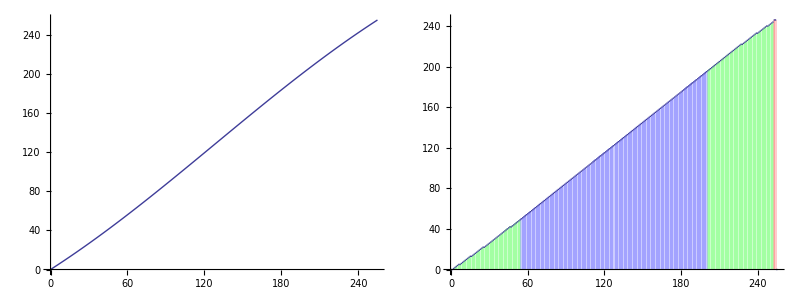

```mathematica
setUprErf[ gMatLAB[[1]],cMatLAB[[1]],0,255,0,255]
Grid[{{Plot[nErf[x],{x,0,255}],
DiscretePlot[Evaluate[Floor[pErf[x]]],{x,0,255,1},ExtentSize->Full,ColorFunction->pErfColor,ColorFunctionScaling->False,Joined->False]}}]
```

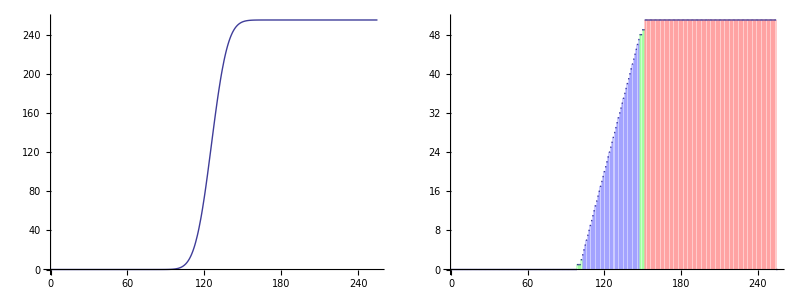

```mathematica
setUprErf[ gMatLAB[[2]],cMatLAB[[2]],0,255,0,255]
Grid[{{Plot[nErf[x],{x,0,255}],
DiscretePlot[Evaluate[Floor[pErf[x]]],{x,0,255,1},ExtentSize->Full,ColorFunction->pErfColor,ColorFunctionScaling->False,Joined->False]}}]
```

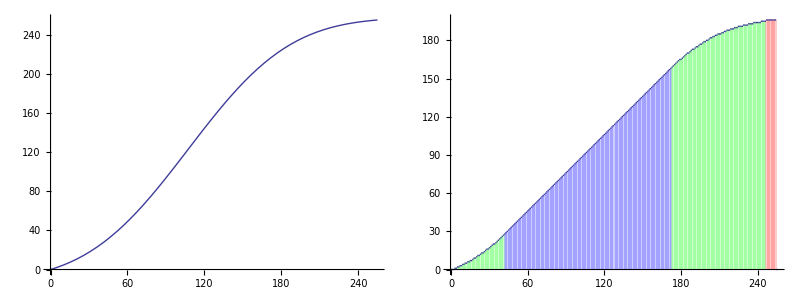

```mathematica
setUprErf[ gMatLAB[[3]],cMatLAB[[3]],0,255,0,255]
Grid[{{Plot[nErf[x],{x,0,255}],
DiscretePlot[Evaluate[Floor[pErf[x]]],{x,0,255,1},ExtentSize->Full,ColorFunction->pErfColor,ColorFunctionScaling->False,Joined->False]}}]
```

```mathematica
setUprErf[ 8,140,0,255,0,255]
TableForm[{{"ErfA", "ErfB", "shift", "scale"},{ErfA, ErfB, shift, scale},{N[ErfA], N[ErfB], N[shift],N[ scale]}}]
iErf[x]
```

ErfA | ErfB | shift | scale
Erf[224/51] | Erf[184/51]+Erf[224/51] | (255 Erf[224/51])/(Erf[184/51]+Erf[224/51]) | 255/(Erf[184/51]+Erf[224/51])
1. | 2. | 127.5 | 127.5

127+127 Erf[8/255 (-140+x)]

```mathematica
N[linear[sUnitGrad[[2]]]- dUnitGrad[[2]]]
```

-155.633

```mathematica
Definition[pErfColor]
```

pErfColor[x_,y_]:=Which[x<pErfBounds⟦1⟧,Red,pErfBounds⟦1⟧≤x<pErfBounds⟦2⟧,Green,pErfBounds⟦2⟧≤x<pErfBounds⟦3⟧,Blue,pErfBounds⟦3⟧≤x<pErfBounds⟦4⟧,Green,pErfBounds⟦4⟧≤x,Red]

```mathematica
pErfBounds
```

{23.,82.,198.,246.}

```mathematica
pErfColor[250,1]
```

RGBColor[1,0,0]

```mathematica
pErf[197.8]
```

140.989

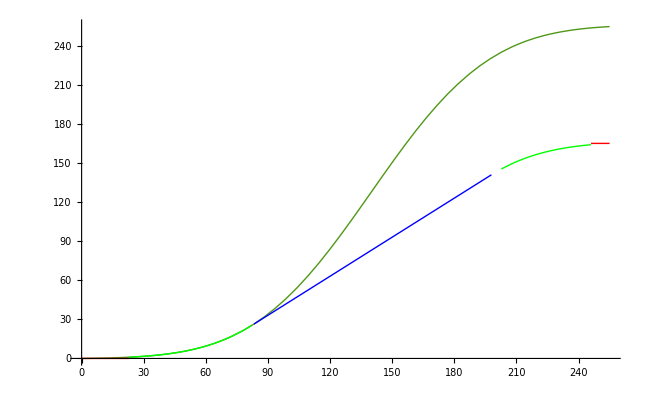

```mathematica
Plot[{nErf[x],pErf[x]},{x,0,255},ColorFunction->Function[{x,y},pErfColor[x,y]],ColorFunctionScaling->False]
```

```mathematica
N[sUnitGrad][[1]]
N[sUnitGrad][[2]]
iErf[N[sUnitGrad][[1]]]
iErf[N[sUnitGrad][[1]]+1]
iErf[N[sUnitGrad][[2]]]
iErf[N[sUnitGrad][[2]]+1]
```

100.

180.

9.64534

10.6135

244.355

245.25

```mathematica
iErf[N[unitGrad][[1]]]
```

397.054

```mathematica
Manipulate[
DiscretePlot[{Evaluate[setUprErf[ g,c,sMin,sMax,dMin,dMax]];Floor[iErf[x]]},{x,sMin,sMax},PlotStyle->{Blue},AxesLabel->TraditionalForm/@{a,iErf[a]},PlotRange->{{sMin,sMax},{dMin, dMax}},Filling->Bottom,
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,dMax},{sMax,dMax}}], Line[{{sMin,dMin},{sMax,dMin}}]}],
{dMin,-255,255,1,ValueThumbSlider[##]&},{{dMax,255},1,255,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{{c,(sMax+sMin)/2},sMin,sMax,1,ValueThumbSlider[##]&},{{g,3},1,10,ValueThumbSlider[##]&}
]
```

```mathematica
Piecewise[{{erf[(g*(-c+x)),(xMax-xMin)],x≥c},{-erf[(g*(c-x)),(xMax-xMin)],x<c}}]
```

```mathematica
Manipulate[
DiscretePlot[{Floor[aErf[x, g,c,sMin,sMax,dMin,dMax]]},{x,sMin,sMax},PlotStyle->{Blue},AxesLabel->TraditionalForm/@{x,Φ[x]},PlotRange->{{sMin,sMax},{dMin, dMax}},Filling->Bottom,
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,dMax},{sMax,dMax}}], Line[{{sMin,dMin},{sMax,dMin}}]}],
{dMin,0,255,1,ValueThumbSlider[##]&},{{dMax,255},1,255,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{{c,(sMax+sMin)/2},sMin,sMax,1,ValueThumbSlider[##]&},{{g,1},1,10,ValueThumbSlider[##]&}
]
```

## Relationship to the Normal Distribution

We want to specify μ, σ, sMin, sMax, dMin, dMax for the space as these are the parameters which can be statistically found.
From these parameters we want to find g and c for the adjustable distribution above.
First we find a relationship to a gaussian on the axis.

```mathematica
Clear[μ,σ, g,c, sMin, sMax, dMin, dMax];
xScale =  1/2 (Erf[(μ - sMin)/(√2 σ)]+Erf[ (sMax - μ)/(√2 σ)]);
anyliticalErf[x_]:=Evaluate[FullSimplify[Integrate[ (dMax-dMin) PDF[NormalDistribution[μ,σ] ,xScale t],{t,sMin / xScale,x / xScale}]]+ dMin]
anyliticalErf[x]
```

dMin+((dMax-dMin) (Erf[(-sMin+μ)/(√2 σ)]-Erf[(-x+μ)/(√2 σ)]))/(Erf[(sMax-μ)/(√2 σ)]+Erf[(-sMin+μ)/(√2 σ)])

Comparing to the adjustable distribution

```mathematica
Clear[μ,σ, g,c, sMin, sMax, dMin, dMax];
setUprErf[ g,c,sMin,sMax,dMin,dMax]
nErf[x] /.{Erf[(g (c-x))/(sMax-sMin)]->- Erf[(g (x-c))/(sMax-sMin)]};
%[[0]][%[[1]],Simplify[Together[%[[0]][%[[2]],%[[3]]]]]]
```

dMin+((dMax-dMin) (Erf[(g (c-sMin))/(sMax-sMin)]+Erf[(g (-c+x))/(sMax-sMin)]))/(Erf[(g (-c+sMax))/(sMax-sMin)]+Erf[(g (c-sMin))/(sMax-sMin)])

We can see the relationship of the average to c and the standard deviation to g.

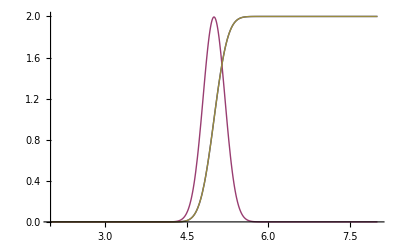

```mathematica
μ =5;
σ =.2;
sMax = 8; sMin = 2;
dMin = 0; dMax= 2;

g =  (sMax-sMin)/(Sqrt[2] σ) ;
c = μ;

setUprErf[ g,c,sMin,sMax,dMin,dMax]
Plot[{anyliticalErf[x],PDF[NormalDistribution[μ,σ],x], nErf[x]},{x,sMin, sMax},PlotRange->{{sMin, sMax},Automatic}]
```

```mathematica
g
```

194.722

```mathematica
Manipulate[
Plot[{Evaluate[g =  (sMax-sMin)/(Sqrt[2] σ) ;setUprErf[ g,μ,sMin,sMax,dMin,dMax]];nErf[x],anyliticalErf[x],(dMax-dMin) PDF[NormalDistribution[μ,σ],x]},{x,sMin,sMax},PlotStyle->{Blue,Green,Red},AxesLabel->TraditionalForm/@{a,iErf[a]},PlotRange->{{sMin,sMax},{dMin, dMax}},
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,dMax},{sMax,dMax}}], Line[{{sMin,dMin},{sMax,dMin}}]}],
{{dMin,0},-255,255,1,ValueThumbSlider[##]&},{{dMax,255},1,255,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{{μ,128},sMin,sMax,1,ValueThumbSlider[##]&},{{σ,0.5},0.0,10.0,ValueThumbSlider[##]&}
]
```

## Approximations to the Erf

A good approximation is found using continued fractions and the following numbers

```mathematica
Unprotect[Rationalize];
Options[Rationalize]={Precision->10^-12};
Protect[Rationalize];
```

```mathematica
Options[Rat]={Precision->10^-12};
a1=0.254829592;
A1[OptionsPattern[Rat]]:=Rationalize[a1,OptionValue[Precision]];
a2=0.284496736;
A2[OptionsPattern[Rat]]:=Rationalize[a2,OptionValue[Precision]];
a3=1.421413741;
A3[OptionsPattern[Rat]]:=Rationalize[a3,OptionValue[Precision]];
a4=1.453152027;
A4[OptionsPattern[Rat]]:=Rationalize[a4,OptionValue[Precision]];
a5=1.061405429;
A5[OptionsPattern[Rat]]:=Rationalize[a5,OptionValue[Precision]];
p=0.3275911;
P[OptionsPattern[Rat]]:=Rationalize[p,OptionValue[Precision]];
```

```mathematica
TableForm[{{"Precision","A1","A2","A3","A4","A5","P"},Sequence@@Table[pre=10^(-prec);{pre,A1[Precision->pre],A2[Precision->pre],A3[Precision->pre],A4[Precision->pre],A5[Precision->pre],P[Precision->pre]},{prec,1,12}]}]
```

Precision | A1 | A2 | A3 | A4 | A5 | P
1/10 | 1/3 | 1/3 | 3/2 | 3/2 | 1 | 1/3
1/100 | 1/4 | 2/7 | 10/7 | 13/9 | 17/16 | 1/3
1/1000 | 11/43 | 19/67 | 27/19 | 61/42 | 35/33 | 17/52
1/10000 | 13/51 | 31/109 | 172/121 | 93/64 | 121/114 | 19/58
1/100000 | 66/259 | 134/471 | 425/299 | 667/459 | 121/114 | 19/58
1/1000000 | 277/1087 | 167/587 | 1447/1018 | 853/587 | 3215/3029 | 970/2961
1/10000000 | 897/3520 | 701/2464 | 4766/3353 | 5025/3458 | 4667/4397 | 1141/3483
1/100000000 | 3245/12734 | 4740/16661 | 15745/11077 | 18487/12722 | 9697/9136 | 3461/10565
1/1000000000 | 7664/30075 | 6843/24053 | 15745/11077 | 30243/20812 | 9697/9136 | 11543/35236
1/10000000000 | 10909/42809 | 26671/93748 | 150613/105960 | 115094/79203 | 9697/9136 | 11543/35236
1/100000000000 | 62209/244120 | 93699/329350 | 316971/222997 | 514984/354391 | 1420671/1338481 | 446716/1363639
1/1000000000000 | 259745/1019289 | 220912/776501 | 784555/551954 | 1859991/1279970 | 1604914/1512065 | 758377/2315011

The functional Approximation is formed thus

```mathematica
Clear[t,tt,erfP, erfH,erfA,error];
t[x_,opt___Rule]:=1/(1+P[opt] x)
t[a_,b_/;Not[TrueQ[Head[b]==Rule]],opt___Rule]:=b/(b+a*P[opt])
erfP[a_,b_,opt___Rule]:=(((((A5[opt]*t[a,b,opt]-A4[opt])*t[a,b,opt])+A3[opt])*t[a,b,opt]-A2[opt])*t[a,b,opt]+A1[opt])
erfH[a_,b_,opt___Rule]:=1-erfP[a,b,opt]*t[a,b,opt]*Exp[-1*a^2/b^2]
erfA[Times[a_,Power[b_,-1]],opt___Rule]:=Piecewise[{{erfH[a,b,opt],a/b≥0},{-erfH[-a,b],a/b<0}}]
erfA[a_,opt___Rule]:=Piecewise[{{erfH[a,1,opt],a≥0},{-erfH[-a,1],a<0}}]
erfA[a_,b_,opt___Rule]:=Piecewise[{{erfH[a,b,opt],a≥0},{-erfH[-a,b],a<0}}]
error[a_,opt___Rule]:=erfA[a,opt]-Erf[a];
```

```mathematica
Manipulate[
GraphicsRow[{Plot[erfA[x,Precision -> 10^(-prec) ],{x,-2,2},PlotStyle->{Blue},PlotRange->Automatic],
Plot[{error[x/1,Precision -> 10^(-prec)]},{x,-2,2},PlotRange->All]}],
{prec,0,12,1,ValueThumbSlider[##]&}]
```

## Distribution Function

```mathematica
rErf[x, g,c,0,255,0,2^16,Function[{a,b},erfA[a,b,Precision->10^-2]]]
```

rErf[x,g,c,0,255,0,65536,Function[{a,b},erfA[a,b,Precision→1/10^2]]]

```mathematica
Manipulate[
GraphicsRow[{Plot[{Floor[irErf[x, g,c,sMin,sMax,0,2^dMaxBits,Function[{a,b},erfA[a,b,Precision->10^(-precision)]]]]},{x,sMin,sMax},PlotStyle->{Blue},AxesLabel->TraditionalForm/@{x,Φ[x]},PlotRange->{{sMin,sMax},{0, 2^dMaxBits}},Filling->Bottom,PlotPoints->sMax-sMin+1,
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,2^dMaxBits},{sMax,2^dMaxBits}}], Line[{{sMin,0},{sMax,0}}]}],
Plot[{rErf[x, g,c,sMin,sMax,0,2^dMaxBits,Function[{a,b},erfA[a,b,Precision->10^(-precision)]]] - rErf[x, g,c,sMin,sMax,0,2^dMaxBits]},{x,sMin,sMax},PlotStyle->{Blue},AxesLabel->"Error",PlotRange->All,Filling->Axis,PlotPoints->sMax-sMin+1]}],{{precision,12},1,12,1,ValueThumbSlider[##]&},{{dMaxBits,16},1,64,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{{c,(sMax+sMin)/2},sMin,sMax,1,ValueThumbSlider[##]&},{{g,1},1,10,ValueThumbSlider[##]&}
]
```

```mathematica
Clear[t,tt,erfP, erfH,erfA,error];
it[a_,b_,opt___Rule]:=b/(b+a*P[opt])
erfP[a_,b_,opt___Rule]:=(((((A5[opt]*t[a,b,opt]-A4[opt])*t[a,b,opt])+A3[opt])*t[a,b,opt]-A2[opt])*t[a,b,opt]+A1[opt])
erfH[a_,b_,opt___Rule]:=1-erfP[a,b,opt]*t[a,b,opt]*Exp[-1*a^2/b^2]
erfA[Times[a_,Power[b_,-1]],opt___Rule]:=Piecewise[{{erfH[a,b,opt],a/b≥0},{-erfH[-a,b],a/b<0}}]
erfA[a_,opt___Rule]:=Piecewise[{{erfH[a,1,opt],a≥0},{-erfH[-a,1],a<0}}]
erfA[a_,b_/;b≥0,opt___Rule]:=Piecewise[{{erfH[a,b,opt],a≥0},{-erfH[-a,b],a<0}}]
error[a_,opt___Rule]:=erfA[a,opt]-Erf[a];
```

```mathematica
Clear[erfH,erfHs,yRange]
erfH[a_]:=yRange-yRange(((((aa5 tt[a]-aa4) tt[a])+aa3) tt[a]-aa2) tt[a]+aa1) tt[a]
erfHs[a_]:=yRange-(((((aa5 yRange^(1/16) tt[a]-aa4 yRange^(1/16)) yRange^(1/16) tt[a])+aa3 yRange^(1/8) ) yRange^(1/8) tt[a]-aa2 yRange^(1/4)) yRange^(1/4) tt[a]+aa1 yRange^(1/2)) yRange^(1/2)tt[a]
```

```mathematica
Simplify[erfHs[x]]
Simplify[erfH[x]]
```

yRange (1-aa1 tt[x]+aa2 tt[x]^2-aa3 tt[x]^3+aa4 tt[x]^4-aa5 tt[x]^5)

```mathematica
erfH[a_]:=yRange-yRange(((((aa5 it[a]-aa4) it[a])+aa3) it[a]-aa2) it[a]+aa1) it[a]*Exp[-1 a^2/xRange^2];
```

```mathematica
erfH[a_]:=yRange-((((( it[a,aa5N  yRange^(1/16),aa5D]-aa4 yRange^(1/16)) yRange^(1/16) it[a])+aa3 yRange^(1/8) ) yRange^(1/8) it[a]-aa2 yRange^(1/4)) yRange^(1/4) it[a]+aa1 yRange^(1/2)) yRange^(1/2)it[a];
```

yRange-yRange tt[x] (aa1+tt[x] (-aa2+tt[x] (aa3-aa4 tt[x]+aa5 tt[x]^2)))

```mathematica
Clear[setUprErf];
setUprErf[ g_,c_,xMin_,xMax_,yMin_,yMax_,prec_]:=Module[{aa5,aa4,aa3,aa2,aa1,ppD,ppN},
Clear[yRange,xRange, erfN,erfD, it,erfH,rErf];
yRange = yMax-yMin;
xRange = xMax-xMin;
erfN = Erf[g (c-xMin)/xRange];
erfD = Erf[g (-c+xMax)/xRange]+Erf[g (c-xMin)/xRange];
ReplaceAll[
Unevaluated[
it[a_,n_,d_]:= n ppD xRange/(d(ppD xRange+a ppN));
erfH[a_]:=yRange-((((( it[a,aa4D aa5N  yRange^(1/16),aa5D]-aa4N yRange^(1/16))  it[a,aa3D yRange^(1/16),aa4D])+aa3N yRange^(1/8) )  it[a, aa2D yRange^(1/8), aa3D]-aa2N yRange^(1/4))  it[a,aa1D yRange^(1/4),aa2D]+aa1N yRange^(1/2))it[a, yRange^(1/2),aa1D];
rErf[x_]:=yMin+(   ( Sign[x-c]  erfH[grad Abs[x-const]] + yRange erfN))/ erfD;]
,{ppN->Numerator[P[Precision->prec]],ppD->Denominator[P[Precision->prec]],aa1->A1[Precision->prec],aa2->A2[Precision->prec],aa3->A3[Precision->prec],aa4->A4[Precision->prec],aa5->A5[Precision->prec],
aa1N->Numerator[A1[Precision->prec]],aa2N->Numerator[A2[Precision->prec]],aa3N->Numerator[A3[Precision->prec]],aa4N->Numerator[A4[Precision->prec]],aa5N->Numerator[A5[Precision->prec]], 
aa1D->Denominator[A1[Precision->prec]],aa2D->Denominator[A2[Precision->prec]],aa3D->Denominator[A3[Precision->prec]],aa4D->Denominator[A4[Precision->prec]],aa5D->Denominator[A5[Precision->prec]],const -> c,grad -> g}];
]
```

```mathematica
setUprErf[ 2,128,0,255,0,128,0.001]
```

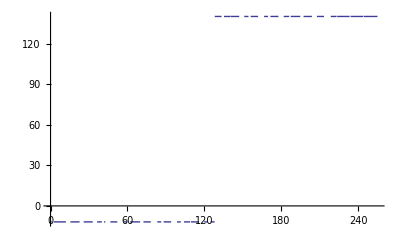

```mathematica
Plot[rErf[x],{x,0,255},PlotRange->All]
```

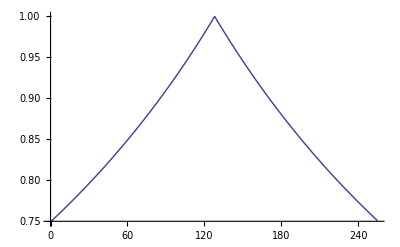

```mathematica
Plot[it[2 Abs[x-128]],{x,0,255},PlotRange->All]
```

## Difficult to round so

```mathematica
c1 = (a1 - a2 + a3 - a4 + a5);
C1[OptionsPattern[Rat]]:=Rationalize[c1,OptionValue[Precision]];
c2 = p (4*a1 - 3*a2 + 2*a3 - a4);
C2[OptionsPattern[Rat]]:=Rationalize[c2,OptionValue[Precision]];
c3 = (6*a1 - 3*a2 + a3)*p^2 ;
C3[OptionsPattern[Rat]]:=Rationalize[c3,OptionValue[Precision]];
c4 = (4*a1 - a2)*p^3;
C4[OptionsPattern[Rat]]:=Rationalize[c4,OptionValue[Precision]];
c5 = a1*p^4;
C5[OptionsPattern[Rat]]:=Rationalize[c5,OptionValue[Precision]];
```

```mathematica
TableForm[{{"Precision","C1","C2","C3","C4","C5","P"},Sequence@@Table[pre=10^(-prec);{pre,C1[Precision->pre],C2[Precision->pre],C3[Precision->pre],C4[Precision->pre],C5[Precision->pre],P[Precision->pre]},{prec,1,12}]}]
```

Precision | C1 | C2 | C3 | C4 | C5 | P
1/10 | 1 | 1/2 | 1/4 | 0 | 0 | 1/3
1/100 | 1 | 1/2 | 2/9 | 1/38 | 0 | 1/3
1/1000 | 1 | 25/49 | 7/31 | 1/38 | 1/340 | 17/52
1/10000 | 1 | 53/104 | 9/40 | 3/116 | 1/340 | 19/58
1/100000 | 1 | 133/261 | 142/631 | 7/271 | 1/340 | 19/58
1/1000000 | 1 | 213/418 | 178/791 | 31/1200 | 3/1022 | 970/2961
1/10000000 | 1 | 3701/7263 | 365/1622 | 100/3871 | 4/1363 | 1141/3483
1/100000000 | 1 | 4979/9771 | 2003/8901 | 162/6271 | 23/7837 | 3461/10565
1/1000000000 | 999999916/999999917 | 15363/30149 | 6739/29947 | 162/6271 | 157/53496 | 11543/35236
1/10000000000 | 999999916/999999917 | 51281/100636 | 22585/100364 | 18985/734907 | 226/77007 | 11543/35236
1/100000000000 | 999999916/999999917 | 189761/372395 | 61016/271145 | 32107/1242858 | 1785/608219 | 446716/1363639
1/1000000000000 | 999999916/999999917 | 430803/845426 | 205633/913799 | 34537/1336923 | 3141/1070261 | 758377/2315011

```mathematica
Clear[t,erfPC, erfHC,erfA,error];
t[x_,OptionsPattern[Rat]]:=1/(1+P[Precision->OptionValue[Precision]] x)
t[a_,b_,OptionsPattern[Rat]]:=b/(b+a*P[Precision->OptionValue[Precision]])
erfPC[a_,b_,OptionsPattern[Rat]]:=(C1[Precision->OptionValue[Precision]] *b^4 + C2[Precision->OptionValue[Precision]]a*b^3 + C3[Precision->OptionValue[Precision]]*a^2*b^2+ C4[Precision->OptionValue[Precision]]*a^3*b + C5[Precision->OptionValue[Precision]]*a^4)/
 (b + a*P[Precision->OptionValue[Precision]])^4
erfHC[a_,b_,OptionsPattern[Rat]]:=1-erfPC[a,b,Precision->OptionValue[Precision]]*t[a,b,Precision->OptionValue[Precision]]*Exp[-1*a^2/b^2]
erfC[a_,b_/;b≥0,OptionsPattern[Rat]]:=Piecewise[{{erfHC[a,b,Precision->OptionValue[Precision]],a≥0},{-erfHC[-a,b,Precision->OptionValue[Precision]],a<0}}]
error[a_,OptionsPattern[Rat]]:=erfC[a,1,Precision->OptionValue[Precision]]-Erf[a];
```

```mathematica
Manipulate[
GraphicsRow[{Plot[erfC[x,1,Precision -> 10^(-prec) ],{x,-2,2},PlotStyle->{Blue},PlotRange->Automatic],
Plot[{error[x/1,Precision -> 10^(-prec)]},{x,-2,2},PlotRange->All]}],
{prec,1,12,1,ValueThumbSlider[##]&}]
```

```mathematica
Clear[setUprErf];
setUprErf[ g_,c_,xMin_,xMax_,yMin_,yMax_,prec_]:=Module[{cc5,cc4,cc3,cc2,cc1,ppD,ppN},
Clear[yRange,xRange, erfN,erfD, it,erfH,rErf,erfHCa];
yRange = yMax-yMin;
xRange = xMax-xMin;
erfN = Rationalize[N[Erf[g (c-xMin)/xRange]],N[1/yRange]];
erfD =  Rationalize[N[Erf[g (-c+xMax)/xRange]+Erf[g (c-xMin)/xRange]],N[1/yRange]];
ReplaceAll[
Unevaluated[
erfHC[a_,b_]:=1-b ppD( cc1  b^4 +  cc2 a b^3 +  cc3  a^2 b^2+  cc4  a^3 b +  cc5  a^4) Exp[-1 a^2/b^2]/(ppD b + a ppN )^5;

erfHCs[a_]:=1-xxRange ppD^5( cc1  xxRange^4 +  cc2 a xxRange^3 +  cc3  a^2 xxRange^2+  cc4  a^3 xxRange +  cc5  a^4) Exp[-1 a^2/xxRange^2]/(ppD xxRange + a ppN )^5;

erfHCa[a_]:=1-xxRange ppD^5( cc1  xxRange^4 +  cc2 a xxRange^3 +  cc3  a^2 xxRange^2+  cc4  a^3 xxRange +  cc5  a^4) exp/(ppD xxRange + a ppN )^5;
rErf[  x_]:=yMin+yyRange(   ( Sign[x-const]   erfHCs[grad Abs[x-const]] +  erfNN))/ erfDD;
rErfA[x_]:=yMin+yyRange(   ( Sign[x-const]   erfHCa[grad Abs[x-const]] +  erfNN))/ erfDD;
rErfPos[  x_]:=yMin+yyRange(   ( erfHCs[grad x] +  erfNN))/ erfDD;
rErfAPos[x_]:=yMin+yyRange(   ( erfHCa[grad x] +  erfNN))/ erfDD;
rErfNeg[  x_]:=yMin+yyRange(   ( - erfHCs[grad x] +  erfNN))/ erfDD;
rErfANeg[x_]:=yMin+yyRange(   ( - erfHCa[grad x] +  erfNN))/ erfDD;
],{exp ->Normal[Series[ Exp[-1 a$^2/xRange^2],{a$,0,16AntiSeries[yRange,xRange]}]],ppN->Numerator[P[Precision->prec]],ppD->Denominator[P[Precision->prec]],cc1->C1[Precision->prec],cc2->C2[Precision->prec],cc3->C3[Precision->prec],cc4->C4[Precision->prec],cc5->C5[Precision->prec],
cc1N->Numerator[C1[Precision->prec]],cc2N->Numerator[C2[Precision->prec]],cc3N->Numerator[C3[Precision->prec]],cc4N->Numerator[C4[Precision->prec]],cc5N->Numerator[C5[Precision->prec]], 
cc1D->Denominator[C1[Precision->prec]],cc2D->Denominator[C2[Precision->prec]],cc3D->Denominator[C3[Precision->prec]],cc4D->Denominator[C4[Precision->prec]],cc5D->Denominator[C5[Precision->prec]],const -> c,grad -> g,erfNN ->erfN,erfDD->erfD,yyRange -> yMax-yMin, xxRange->xMax-xMin}];
Clear[erfSE,rErfSE,rErfSEH];
ReplaceAll[
Unevaluated[erfSE[a_]:=fun],{fun->Normal[Series[Expand[Apart[erfHCs[a]]],{a,0,3}]]}];
ReplaceAll[
Unevaluated[rErfSEPos[a_]:=fun],{fun->Normal[Series[Expand[Apart[rErfPos[a]]],{a,0,10}]]}];
ReplaceAll[
Unevaluated[rErfSENeg[a_]:=fun],{fun->Normal[Series[Expand[Apart[rErfNeg[a]]],{a,0,10}]]}];
rErfSE[a_]=Piecewise[{{rErfSEPos[a-c],a≥ c},{  rErfSENeg[c-a],a< c}}]
]
```

```mathematica
erfD
```

27/14

```mathematica
rErfPos[a]
```

1792/27 (49/25-(96952028160 (4228250625+(1243603125 a)/49+(4096575 a^2)/31+(6885 a^3)/38+(81 a^4)/340) ⅇ^(-a^2/7225))/(13260+51 a)^5)

```mathematica
coeffs=CoefficientList[rErfSEPos[a],a]
N[%]
```

{14336/225,12224/13923,328624/7153985475,-17124932/420722479125,-46626166954/14107340110098178125,127031924587/73358168572510526250,-191870835866471/413409958990383070681875000,-372998130031907/7165772622499973225152500000,-189514574106065141/16153084645639439644138765500000000,157547612795400923/107687230970929597627591770000000000,7148799450584122013/24274855605466949897211736793400000000000}

{63.7156,0.877972,0.0000459358,-0.0000407036,-3.3051×10^-9,1.73167×10^-9,-4.64118×10^-13,-5.20527×10^-14,-1.17324×10^-17,1.46301×10^-18,2.94494×10^-22}

```mathematica
coeffsRootA=Table[Rationalize[N[coeffs[[n]]^(2/(n-1))],N[1/xRange^2]],{n,3,Length[coeffs]}]
```

{1/21769,-1/1690+ⅈ/975,ⅈ/17394,1/3196,1/25831+ⅈ/14913,1/10010+ⅈ/7983,1/24163+ⅈ/24163,1/9189,1/20238}

```mathematica
rErfSE[a]
```

Piecewise[{{14336/225+(12224 (-128+a))/13923+(328624 (-128+a)^2)/7153985475-(17124932 (-128+a)^3)/420722479125, a≥128}, {14336/225-(12224 (128-a))/13923-(328624 (128-a)^2)/7153985475+(17124932 (128-a)^3)/420722479125, a<128}, {0, True}}]

```mathematica
setUprErf[ 3,128,0,255,0,128,0.001]
```

Series::serlim: Series order specification 16\ AntiSeries[128, 255] is not a machine-sized integer.

Piecewise[{{14336/225+(12224 (-128+a$))/13923+(328624 (-128+a$)^2)/7153985475-(17124932 (-128+a$)^3)/420722479125-(46626166954 (-128+a$)^4)/14107340110098178125+(127031924587 (-128+a$)^5)/73358168572510526250-(191870835866471 (-128+a$)^6)/413409958990383070681875000-(372998130031907 (-128+a$)^7)/7165772622499973225152500000-(189514574106065141 (-128+a$)^8)/16153084645639439644138765500000000+(157547612795400923 (-128+a$)^9)/107687230970929597627591770000000000+(7148799450584122013 (-128+a$)^10)/24274855605466949897211736793400000000000, a$≥128}, {14336/225-(12224 (128-a$))/13923-(328624 (128-a$)^2)/7153985475+(17124932 (128-a$)^3)/420722479125+(46626166954 (128-a$)^4)/14107340110098178125-(127031924587 (128-a$)^5)/73358168572510526250+(191870835866471 (128-a$)^6)/413409958990383070681875000+(372998130031907 (128-a$)^7)/7165772622499973225152500000+(189514574106065141 (128-a$)^8)/16153084645639439644138765500000000-(157547612795400923 (128-a$)^9)/107687230970929597627591770000000000-(7148799450584122013 (128-a$)^10)/24274855605466949897211736793400000000000, a$<128}, {0, True}}]

```mathematica
aErf[x, 3,128,0,255,0,128]
```

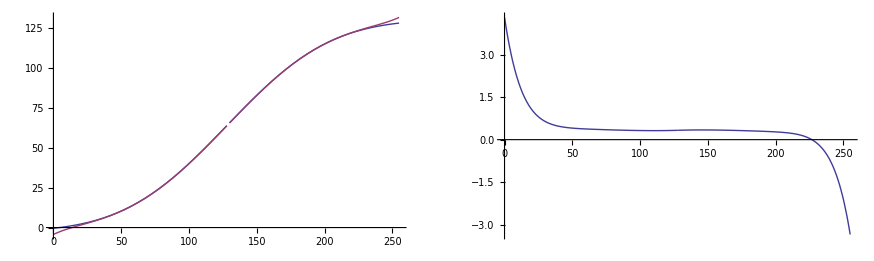

```mathematica
GraphicsRow[{Plot[{N[rErf[x]],N[rErfSE[x]]},{x,0,255},PlotRange->All],Plot[N[aErf[x, 3,128,0,255,0,128]]-N[rErfSE[x]],{x,0,255},PlotRange->All]}]
```

```mathematica
rErf[x_, g_,c_,xMin_,xMax_,yMin_,yMax_,erf_:Function[{a,b},Erf[a,b]]]:=yMin+((yMax-yMin) (Piecewise[{{erf[(g (-c+x)),(xMax-xMin)],x≥c},{-erf[(g (c-x)),(xMax-xMin)],x<c}}]+erf[(g (c-xMin)),(xMax-xMin)]))/( erf[(g (-c+xMax)),(xMax-xMin)]+erf[(g (c-xMin)),(xMax-xMin)]);
```

## Series Expansion

```mathematica
Unprotect[Erf];
Erf[a_,b_]:=Erf[a/b];
Protect[Erf];
```

```mathematica
aErf[x_, g_,c_,xMin_,xMax_,yMin_,yMax_,erf_:Function[{a,b},Erf[a,b]]]:=yMin+((yMax-yMin)*(Piecewise[{{erf[(g*(-c+x)),(xMax-xMin)],x≥c},{-erf[(g*(c-x)),(xMax-xMin)],x<c}}]+erf[(g*(c-xMin)),(xMax-xMin)]))/( erf[(g*(-c+xMax)),(xMax-xMin)]+erf[(g*(c-xMin)),(xMax-xMin)]);
```

```mathematica
Clear[setUprErf];
setUprErf[ g_,c_,xMin_,xMax_,yMin_,yMax_,prec_]:=Module[{const ,grad ,erfNN ,erfDD,yyRange, xxRange},
Clear[yRange,xRange, erfN,erfD,rErfPos,rErfNeg,coeffs,coeffsRoot,coeffsRootA];
yRange = yMax-yMin;
xRange = xMax-xMin;
erfN = Rationalize[N[Erf[g (   c-xMin)/xRange]],N[1/yRange]];
erfD = Rationalize[N[Erf[g (-c+xMax)/xRange]+Erf[g (c-xMin)/xRange]],N[1/yRange]];
ReplaceAll[
Unevaluated[
rErfPos[  x_]:=yMin+yyRange( (    Erf[grad x/xxRange] +  erfNN))/ erfDD;
rErfNeg[  x_]:=yMin+yyRange( ( - Erf[grad x/xxRange] +  erfNN))/ erfDD;
],{const -> c,grad -> g,erfNN ->erfN,erfDD->erfD,yyRange -> yMax-yMin, xxRange->xMax-xMin}];
Clear[rErfSEPos,rErfSENeg,rErfSE];
ReplaceAll[
Unevaluated[rErfSEPos[a_]:=fun],{fun->Normal[Series[Expand[Apart[rErfPos[a]]],{a,0,20}]]}];
ReplaceAll[
Unevaluated[rErfSENeg[a_]:=fun],{fun->Normal[Series[Expand[Apart[rErfNeg[a]]],{a,0,20}]]}];
rErfSE[a_]=Piecewise[{{rErfSEPos[a-c],a≥ c},{  rErfSENeg[c-a],a< c}}];
coeffs=Abs[CoefficientList[rErfSEPos[a],a]];
coeffsRoot=Table[pow =Abs[2n-3];Simplify[coeffs[[n]]^(1/pow)],{n,1,Length[coeffs]}];
coeffsRootA=Table[Rationalize[N[coeffsRoot[[n]]],N[1/xRange^2]],{n,1,Length[coeffs]}];
]
setUprErf[ 3,128,0,255,0,128,0.001]
rErfSE[a]
```

Piecewise[{{14336/225+(3584 (-128+a))/(2295 √π)-(3584 (-128+a)^3)/(49744125 √π)+(1792 (-128+a)^5)/(599002171875 √π)-(256 (-128+a)^7)/(2596674415078125 √π)+(448 (-128+a)^9)/(168848753840455078125 √π)-(448 (-128+a)^11)/(7455141506372315185546875 √π)+(224 (-128+a)^13)/(190970227087096282855224609375 √π)-(32 (-128+a)^15)/(1592030643120312281110382080078125 √π)+(4 (-128+a)^17)/(13036077582750157061825511932373046875 √π)-(4 (-128+a)^19)/(947396938326367664468169079685211181640625 √π), a≥128}, {14336/225-(3584 (128-a))/(2295 √π)+(3584 (128-a)^3)/(49744125 √π)-(1792 (128-a)^5)/(599002171875 √π)+(256 (128-a)^7)/(2596674415078125 √π)-(448 (128-a)^9)/(168848753840455078125 √π)+(448 (128-a)^11)/(7455141506372315185546875 √π)-(224 (128-a)^13)/(190970227087096282855224609375 √π)+(32 (128-a)^15)/(1592030643120312281110382080078125 √π)-(4 (128-a)^17)/(13036077582750157061825511932373046875 √π)+(4 (128-a)^19)/(947396938326367664468169079685211181640625 √π), a<128}, {0, True}}]

```mathematica
Expand[funP[[1]]/a]
```

3584/2295-(3584 a^2)/49744125+(1792 a^4)/599002171875-(256 a^6)/2596674415078125+(448 a^8)/168848753840455078125-(448 a^10)/7455141506372315185546875+(224 a^12)/190970227087096282855224609375-(32 a^14)/1592030643120312281110382080078125+(4 a^16)/13036077582750157061825511932373046875-(4 a^18)/947396938326367664468169079685211181640625

```mathematica
rErfSEPos[a];
coeffsTemp=CoefficientList[rErfSEPos[a],a];
scalar = coeffsTemp[[1]];
coeffs = Take[coeffsTemp,{2,Length[coeffsTemp]}];
coeffsSign=Sign[coeffs];
coeffsAbs=Abs[coeffs];
coeffsRoot=Table[Simplify[coeffsAbs[[n]]^(1/n)],{n,1,Length[coeffsAbs]}];
coeffsRootA=Map[Rationalize[N[#],N[1/yRange^4]]&,coeffsRoot];
coeffsError = N[coeffsRootA - coeffsRoot];
TableForm[{coeffs,coeffsRoot,coeffsRootA,coeffsError}]
```

3584/(2295 √π) | 0 | -3584/(49744125 √π) | 0 | 1792/(599002171875 √π) | 0 | -256/(2596674415078125 √π) | 0 | 448/(168848753840455078125 √π) | 0 | -448/(7455141506372315185546875 √π) | 0 | 224/(190970227087096282855224609375 √π) | 0 | -32/(1592030643120312281110382080078125 √π) | 0 | 4/(13036077582750157061825511932373046875 √π) | 0 | -4/(947396938326367664468169079685211181640625 √π)
3584/(2295 √π) | 0 | (8 7^(1/3))/(255 3^(1/3) π^(1/6)) | 0 | (2 (2/3)^(3/5) (7/5)^(1/5))/(85 π^(1/10)) | 0 | (2 2^(1/7))/(85 3^(4/7) π^(1/14)) | 0 | ((2/3)^(2/3) 7^(1/9))/(85 π^(1/18)) | 0 | ((7/55)^(1/11) 2^(6/11))/(85 3^(4/11) π^(1/22)) | 0 | ((7/65)^(1/13) (2/3)^(5/13))/(85 π^(1/26)) | 0 | 2^(1/3)/(85 3^(2/5) 5^(2/15) π^(1/30)) | 0 | 2^(2/17)/(85 3^(5/17) 85^(1/17) π^(1/34)) | 0 | 2^(2/19)/(85 3^(7/19) 95^(1/19) π^(1/38))
9816/11141 | 0 | 693/20155 | 0 | 91/5171 | 0 | 455/35608 | 0 | 206/19697 | 0 | 622/68627 | 0 | 61/7517 | 0 | 311/41923 | 0 | 105/15263 | 0 | 71/11014
1.45901×10^-9 | 0. | 7.32245×10^-10 | 0. | -3.23495×10^-9 | 0. | -3.45676×10^-9 | 0. | -2.67243×10^-9 | 0. | 3.58156×10^-9 | 0. | 1.84623×10^-9 | 0. | -3.50777×10^-9 | 0. | 1.48517×10^-9 | 0. | -6.43088×10^-10

```mathematica
coeffsTemp
```

{14336/225,3584/(2295 √π),0,-3584/(49744125 √π),0,1792/(599002171875 √π),0,-256/(2596674415078125 √π),0,448/(168848753840455078125 √π),0,-448/(7455141506372315185546875 √π),0,224/(190970227087096282855224609375 √π),0,-32/(1592030643120312281110382080078125 √π),0,4/(13036077582750157061825511932373046875 √π),0,-4/(947396938326367664468169079685211181640625 √π)}

```mathematica
rErfSEPos[a]
```

14336/225+(3584 a)/(2295 √π)-(3584 a^3)/(49744125 √π)+(1792 a^5)/(599002171875 √π)-(256 a^7)/(2596674415078125 √π)+(448 a^9)/(168848753840455078125 √π)-(448 a^11)/(7455141506372315185546875 √π)+(224 a^13)/(190970227087096282855224609375 √π)-(32 a^15)/(1592030643120312281110382080078125 √π)+(4 a^17)/(13036077582750157061825511932373046875 √π)-(4 a^19)/(947396938326367664468169079685211181640625 √π)

{(9816 x)/11141,0,-(693 x)/20155,0,(91 x)/5171,0,-(455 x)/35608,0,(206 x)/19697,0,-(622 x)/68627,0,(61 x)/7517,0,-(311 x)/41923,0,(105 x)/15263,0,-(71 x)/11014}

Piecewise[{{erf[g (-c+x),xMax-xMin], x≥c}, {-erf[g (c-x),xMax-xMin], x<c}, {0, True}}]

Piecewise[{{14336/225+(3584 (-128+x))/(2295 √π)-(3584 (-128+x)^3)/(49744125 √π)+(1792 (-128+x)^5)/(599002171875 √π)-(256 (-128+x)^7)/(2596674415078125 √π)+(448 (-128+x)^9)/(168848753840455078125 √π)-(448 (-128+x)^11)/(7455141506372315185546875 √π)+(224 (-128+x)^13)/(190970227087096282855224609375 √π)-(32 (-128+x)^15)/(1592030643120312281110382080078125 √π)+(4 (-128+x)^17)/(13036077582750157061825511932373046875 √π)-(4 (-128+x)^19)/(947396938326367664468169079685211181640625 √π), x≥128}, {14336/225-(3584 (128-x))/(2295 √π)+(3584 (128-x)^3)/(49744125 √π)-(1792 (128-x)^5)/(599002171875 √π)+(256 (128-x)^7)/(2596674415078125 √π)-(448 (128-x)^9)/(168848753840455078125 √π)+(448 (128-x)^11)/(7455141506372315185546875 √π)-(224 (128-x)^13)/(190970227087096282855224609375 √π)+(32 (128-x)^15)/(1592030643120312281110382080078125 √π)-(4 (128-x)^17)/(13036077582750157061825511932373046875 √π)+(4 (128-x)^19)/(947396938326367664468169079685211181640625 √π), x<128}, {0, True}}]

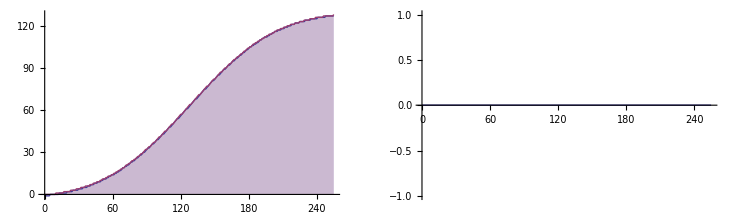

```mathematica
x coeffsRootA coeffsSign
Piecewise[{{erf[(g (-c+x)),(xMax-xMin)],x≥c},{-erf[(g (c-x)),(xMax-xMin)],x<c}}]
funcPos[x_]:=scalar +Plus@@MapIndexed[#1^(First[#2])&,x coeffsRoot coeffsSign]
funcNeg[x_]:=scalar -Plus@@MapIndexed[#1^(First[#2])&,x coeffsRoot coeffsSign]
func[x_]:=Piecewise[{{funcPos[x-128],x≥128},{funcNeg[128-x],x<128}}]
func[x]
GraphicsRow[{DiscretePlot[{Floor[N[func[x]]],Floor[N[aErf[x,3,128,0,255,0,128]]]},{x,0,255},PlotRange->All],DiscretePlot[Floor[N[aErf[x, 3,128,0,255,0,128]]-N[func[x]]],{x,0,255},PlotRange->All]}]
```

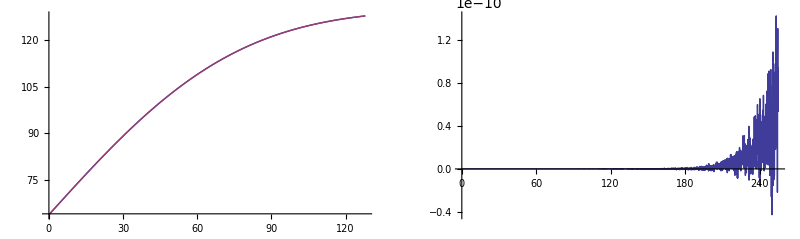

```mathematica
GraphicsRow[{Plot[{N[func[x]],N[rErfSEPos[x]]},{x,0,128},PlotRange->All],Plot[N[rErfSEPos[x]]-N[func[x]],{x,0,255},PlotRange->All]}]
```

```mathematica
Solve[num^n ≤ max,n,Integers]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

```mathematica
max=255; num = 12;
n=Floor[N[Simplify[Log[max]/Log[num]]]];
num^n
num^(n+1)
```

144

1728

```mathematica
IntegerPower[xMax_,num_,den_,pow_,max_]:=Module[{},
maxNumPow = Floor[N[Log[max]/Log[num xMax]]];
maxDenPow = Floor[N[Log[max]/Log[den]]];
divisionsPerMultiplication = Ceiling[N[Log[num xMax]/Log[max]]];


]
```

```mathematica
coeffsFRootA
```

{}

```mathematica
funF[a_]:=Evaluate[Module[{fun,funP,funR},fun = rErfSEPos[a];funP = Collect[Take[fun,{2,Length[rErfSEPos[a]]}], Pi^(-1/2)];
funR = Expand[funP[[1]]/a];
fun[[1]]+a funP[[2]] funR]]
```

```mathematica
Definition[funF]
```

funF[a_]:=14336/225+1/(√π)a (3584/2295-(3584 a^2)/49744125+(1792 a^4)/599002171875-(256 a^6)/2596674415078125+(448 a^8)/168848753840455078125-(448 a^10)/7455141506372315185546875+(224 a^12)/190970227087096282855224609375-(32 a^14)/1592030643120312281110382080078125+(4 a^16)/13036077582750157061825511932373046875-(4 a^18)/947396938326367664468169079685211181640625)

```mathematica
fun = rErfSEPos[a];
funP = Collect[Take[fun,{2,Length[rErfSEPos[a]]}], Pi^(-1/2)];
funR = Expand[funP[[1]]/a];
fun[[1]]+a funP[[2]] funR
```

14336/225+1/(√π)a (3584/2295-(3584 a^2)/49744125+(1792 a^4)/599002171875-(256 a^6)/2596674415078125+(448 a^8)/168848753840455078125-(448 a^10)/7455141506372315185546875+(224 a^12)/190970227087096282855224609375-(32 a^14)/1592030643120312281110382080078125+(4 a^16)/13036077582750157061825511932373046875-(4 a^18)/947396938326367664468169079685211181640625)

```mathematica
Rationalize[Pi^(-1/2),N[yRange^-4]]
```

4821/8545

```mathematica
coeffs[[2]]
```

3584/(2295 √π)

```mathematica
Unevaluated[pow =If[n>1,1/Abs[2n-3],1,1];Simplify[coeffs[[n]]^pow]]/. n->1
```

14336/225

```mathematica
coeffsF=Abs[CoefficientList[funR,a]];
coeffsFPower=Table[pow =If[n>1,1/Abs[n-1],1,1],{n,1,Length[coeffsF]}];
coeffsFRoot=Table[pow =If[n>1,1/Abs[n-1],1,1];Simplify[coeffsF[[n]]^pow],{n,1,Length[coeffsF]}];
coeffsFRootA=Table[Rationalize[N[coeffsFRoot[[n]]],N[1/xRange^2]],{n,1,Length[coeffsF]}];
CoeffsFRoot[x_]:=Evaluate[Flatten[{coeffsFRootA[[1]],Table[coeffsFRootA[[n]] x,{n,2,Length[coeffsFRootA]}]}]];
CoeffsF[x_]:=Evaluate[Flatten[{coeffsFRootA[[1]],Table[(coeffsFRootA[[n]] x)^(n-1),{n,2,Length[coeffsFRootA]}]}]];
coeffsFError = N[coeffsFRootA - coeffsFRoot];
TableForm[{coeffsF,coeffsFPower,coeffsFRoot,coeffsFRootA,coeffsFError}]
```

3584/2295 | 0 | 3584/49744125 | 0 | 1792/599002171875 | 0 | 256/2596674415078125 | 0 | 448/168848753840455078125 | 0 | 448/7455141506372315185546875 | 0 | 224/190970227087096282855224609375 | 0 | 32/1592030643120312281110382080078125 | 0 | 4/13036077582750157061825511932373046875 | 0 | 4/947396938326367664468169079685211181640625
1 | 1 | 1/2 | 1/3 | 1/4 | 1/5 | 1/6 | 1/7 | 1/8 | 1/9 | 1/10 | 1/11 | 1/12 | 1/13 | 1/14 | 1/15 | 1/16 | 1/17 | 1/18
3584/2295 | 0 | (16 √(14/85))/765 | 0 | (4 (7/17)^(1/4))/(85 3^(3/4) √5) | 0 | (2 2^(1/3))/(85 3^(2/3) 85^(1/6)) | 0 | 1/85 (7/85)^(1/8) (2/3)^(3/4) | 0 | ((7/187)^(1/10) 2^(3/5))/(85 3^(2/5) 5^(1/5)) | 0 | ((7/221)^(1/12) (2/3)^(5/12))/(85 5^(1/6)) | 0 | 2^(5/14)/(85 3^(3/7) 5^(3/14) 17^(1/14)) | 0 | (2/85)^(1/8)/(85 3^(5/16)) | 0 | (2/5)^(1/9)/(85 3^(7/18) 323^(1/18))
114/73 | 0 | 1/118 | 0 | 1/135 | 0 | 1/147 | 0 | 2/315 | 0 | 1/167 | 0 | 2/351 | 0 | 1/184 | 0 | 1/191 | 0 | 1/199
-0.0000119378 | 0. | -0.0000135748 | 0. | 0.0000117395 | 0. | 5.93277×10^-6 | 0. | -3.70097×10^-6 | 0. | -8.2603×10^-6 | 0. | -6.64578×10^-7 | 0. | -9.52624×10^-6 | 0. | 0.0000124573 | 0. | -3.14013×10^-6

```mathematica
FactorInteger[Denominator[coeffsFRootA]]
```

{{{73,1}},{{1,1}},{{2,1},{59,1}},{{1,1}},{{3,3},{5,1}},{{1,1}},{{3,1},{7,2}},{{1,1}},{{3,2},{5,1},{7,1}},{{1,1}},{{167,1}},{{1,1}},{{3,3},{13,1}},{{1,1}},{{2,3},{23,1}},{{1,1}},{{191,1}},{{1,1}},{{199,1}}}

```mathematica
CoeffsFRoot[x]
CoeffsF[x]
```

{114/73,0,x/118,0,x/135,0,x/147,0,(2 x)/315,0,x/167,0,(2 x)/351,0,x/184,0,x/191,0,x/199}

{114/73,0,x^2/13924,0,x^4/332150625,0,x^6/10090298369529,0,(256 x^8)/96935851667000390625,0,x^10/16871927924929095158449,0,(4096 x^12)/3496917589577226791795034339201,0,x^14/50985833350937367259526396379136,0,x^16/3137139824701778779401163099378775041,0,x^18/239527496518885244517374318159129478116401}

```mathematica
Clear[x]
```

```mathematica
N[√π]
```

1.77245

```mathematica
co[x_]:=Evaluate[Flatten[{coeffsFRootA[[1]],Table[coeffsFRootA[[n]] x,{n,2,Length[coeffsFRootA]}]}]]
Definition[co]
```

co[x_]:={114/73,0,x/118,0,x/135,0,x/147,0,(2 x)/315,0,x/167,0,(2 x)/351,0,x/184,0,x/191,0,x/199}

```mathematica
RoundedPolynomialApproxFunR[x_,coeffs_]:=Module[{},
prods = Flatten[{coeffs[[1]],Table[coeffs[[n]] x,{n,2,Length[coeffs]}]}];
fun[[1]]+a funP[[2]] funR
]
```

```mathematica
funR
coeffsFA
```

3584/2295-(3584 a^2)/49744125+(1792 a^4)/599002171875-(256 a^6)/2596674415078125+(448 a^8)/168848753840455078125-(448 a^10)/7455141506372315185546875+(224 a^12)/190970227087096282855224609375-(32 a^14)/1592030643120312281110382080078125+(4 a^16)/13036077582750157061825511932373046875-(4 a^18)/947396938326367664468169079685211181640625

{0,a^2/13924,0,a^4/332150625,0,a^6/10090298369529,0,(256 a^8)/96935851667000390625,0,a^10/16871927924929095158449,0,(4096 a^12)/3496917589577226791795034339201,0,a^14/50985833350937367259526396379136,0,a^16/3137139824701778779401163099378775041,0,a^18/239527496518885244517374318159129478116401}

```mathematica
Table[(coeffsFRootA[[n]] a)^n /a,{n,1,Length[coeffsFRootA]}]
```

{114/73,0,(15625 a^2)/217081801,0,(90224199 a^4)/110771831604224,0,(4782969 a^6)/905824306333433,0,(512000000000 a^8)/17980759982220503815017,0,(31381059609 a^10)/230339304218442143770717,0,(9904578032905937 a^12)/16527494836835198184585997320192,0,(51185893014090757 a^14)/20750374965634314601866066480103424,0,(295147905179352825856 a^16)/31209709320485314764017124510323904157681,0,(1978419655660313589123979 a^18)/57155629504430816618802078994918975878812205409}

```mathematica
coeffsFRoot
coeffsFRootA
```

{14336/225,3584/(2295 √π),0,(2 (2/3)^(4/5) 7^(1/5))/(85^(3/5) π^(1/10)),0,(2^(8/9) 7^(1/9))/(3^(1/3) 5^(2/3) 17^(5/9) π^(1/18)),0,2^(8/13)/(3^(4/13) 85^(7/13) π^(1/26)),0,((2/3)^(6/17) 7^(1/17))/(85^(9/17) π^(1/34)),0,((7/11)^(1/21) 2^(2/7))/(3^(4/21) 5^(4/7) 17^(11/21) π^(1/42)),0,((7/13)^(1/25) (2/3)^(1/5))/(5^(14/25) 17^(13/25) π^(1/50)),0,2^(5/29)/(3^(6/29) 5^(17/29) 17^(15/29) π^(1/58)),0,2^(2/33)/(3^(5/33) 85^(6/11) π^(1/66)),0,2^(2/37)/(3^(7/37) 5^(20/37) 17^(19/37) 19^(1/37) π^(1/74))}

{14336/225,163/185,0,56/423,0,23/217,0,13/136,0,11/123,0,4/47,0,9/110,0,11/139,0,1/13,0,3/40}

```mathematica
coeffsF
coeffsFA
```

{3584/2295,0,-3584/49744125,0,1792/599002171875,0,-256/2596674415078125,0,448/168848753840455078125,0,-448/7455141506372315185546875,0,224/190970227087096282855224609375,0,-32/1592030643120312281110382080078125,0,4/13036077582750157061825511932373046875,0,-4/947396938326367664468169079685211181640625}

{1,(163 a)/185,0,(175616 a^3)/75686967,0,(6436343 a^5)/481170140857,0,(62748517 a^7)/860542568759296,0,(2357947691 a^9)/6443858614676334363,0,(4194304 a^11)/2472159215084012303,0,(2541865828329 a^13)/345227121439310000000000000,0,(4177248169415651 a^15)/139708234283055276457744135264099,0,a^17/8650415919381337933,0,(1162261467 a^19)/2748779069440000000000000000000}

```mathematica
Collect[Take[rErfSEPos[a],{2,Length[rErfSEPos[a]]}], Pi^(-1/2)][[1]]
```

(3584 a)/2295-(3584 a^3)/49744125+(1792 a^5)/599002171875-(256 a^7)/2596674415078125+(448 a^9)/168848753840455078125-(448 a^11)/7455141506372315185546875+(224 a^13)/190970227087096282855224609375-(32 a^15)/1592030643120312281110382080078125+(4 a^17)/13036077582750157061825511932373046875-(4 a^19)/947396938326367664468169079685211181640625

```mathematica
setUprErf[ 3,128,0,255,0,128,0.001]
```

```mathematica
TableForm[{coeffs,coeffsRoot,coeffsRootA}]
```

14336/225 | 3584/(2295 √π) | 0 | 3584/(49744125 √π) | 0 | 1792/(599002171875 √π) | 0 | 256/(2596674415078125 √π) | 0 | 448/(168848753840455078125 √π) | 0 | 448/(7455141506372315185546875 √π) | 0 | 224/(190970227087096282855224609375 √π) | 0 | 32/(1592030643120312281110382080078125 √π) | 0 | 4/(13036077582750157061825511932373046875 √π) | 0 | 4/(947396938326367664468169079685211181640625 √π)
14336/225 | 3584/(2295 √π) | 0 | (2 (2/3)^(4/5) 7^(1/5))/(85^(3/5) π^(1/10)) | 0 | (2^(8/9) 7^(1/9))/(3^(1/3) 5^(2/3) 17^(5/9) π^(1/18)) | 0 | 2^(8/13)/(3^(4/13) 85^(7/13) π^(1/26)) | 0 | ((2/3)^(6/17) 7^(1/17))/(85^(9/17) π^(1/34)) | 0 | ((7/11)^(1/21) 2^(2/7))/(3^(4/21) 5^(4/7) 17^(11/21) π^(1/42)) | 0 | ((7/13)^(1/25) (2/3)^(1/5))/(5^(14/25) 17^(13/25) π^(1/50)) | 0 | 2^(5/29)/(3^(6/29) 5^(17/29) 17^(15/29) π^(1/58)) | 0 | 2^(2/33)/(3^(5/33) 85^(6/11) π^(1/66)) | 0 | 2^(2/37)/(3^(7/37) 5^(20/37) 17^(19/37) 19^(1/37) π^(1/74))
14336/225 | 163/185 | 0 | 56/423 | 0 | 23/217 | 0 | 13/136 | 0 | 11/123 | 0 | 4/47 | 0 | 9/110 | 0 | 11/139 | 0 | 1/13 | 0 | 3/40

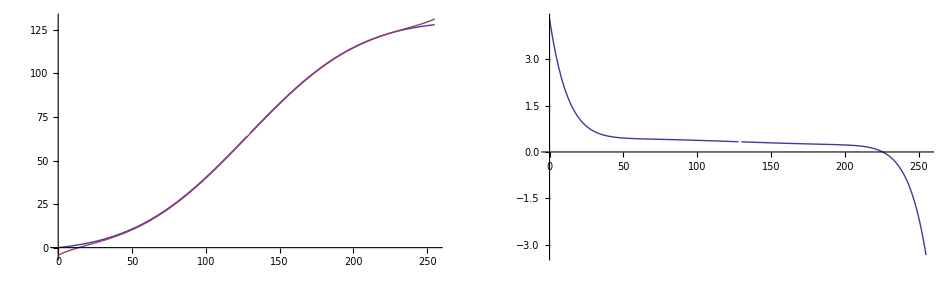

```mathematica
GraphicsRow[{Plot[{N[aErf[x,3,128,0,255,0,128]],N[rErfSE[x]]},{x,0,255},PlotRange->All],Plot[N[aErf[x, 3,128,0,255,0,128]]-N[rErfSE[x]],{x,0,255},PlotRange->All]}]
```

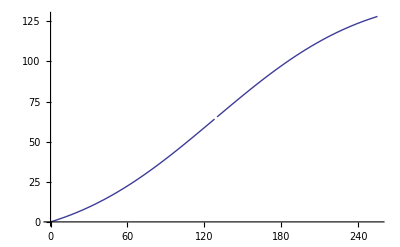

```mathematica
Plot[N[aErf[x,2,128,0,255,0,128]],{x,0,255},PlotRange->Automatic]
```

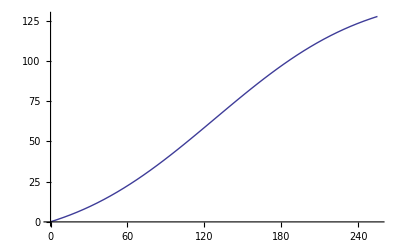

```mathematica
Plot[N[rErfSE[x]],{x,0,255},PlotRange->Automatic]
```

## Approximation of the Exponential Term

```mathematica
AntiFactorial[xx_]:=Module[{i=1,x=xx},While[x>i,x=x/i;i++]; i]
```

```mathematica
Series[ Exp[-a],{a,0,AntiFactorial[255]}]
```

1-a+a^2/2-a^3/6+a^4/24-a^5/120+a^6/720+O[a]^7

Need terms up to 1/yRange so use AntiFactorial to get the series limit. However b is the xRange and xRange>yRange.
The term on the bottom is n!b^2n so we solve yRange < n! b^2n

```mathematica
AntiSeries[xx_,b_]:=Module[{i=1,x=xx},While[xx/(Factorial[i] b^(2 i))>1,i++]; i]
```

```mathematica
Series[ Exp[-1 a^2/2^2],{a,0, 2AntiSeries[255,2]}]
```

1-a^2/4+a^4/32-a^6/384+O[a]^7

```mathematica
Expand[1-b ppD( cc1  b^4 +  cc2 a b^3 +  cc3  a^2 b^2+  cc4  a^3 b +  cc5  a^4) Normal[Series[ Exp[-1 a^2/b^2],{a,0,2 AntiFactorial[255]}]]/(ppD b + a ppN )^5]
```

1-(a^12 cc1 ppD)/(720 b^7 (b ppD+a ppN)^5)+(a^10 cc1 ppD)/(120 b^5 (b ppD+a ppN)^5)-(a^8 cc1 ppD)/(24 b^3 (b ppD+a ppN)^5)+(a^6 cc1 ppD)/(6 b (b ppD+a ppN)^5)-(a^4 b cc1 ppD)/(2 (b ppD+a ppN)^5)+(a^2 b^3 cc1 ppD)/(b ppD+a ppN)^5-(b^5 cc1 ppD)/(b ppD+a ppN)^5-(a^5 cc2 ppD)/(2 (b ppD+a ppN)^5)-(a^13 cc2 ppD)/(720 b^8 (b ppD+a ppN)^5)+(a^11 cc2 ppD)/(120 b^6 (b ppD+a ppN)^5)-(a^9 cc2 ppD)/(24 b^4 (b ppD+a ppN)^5)+(a^7 cc2 ppD)/(6 b^2 (b ppD+a ppN)^5)+(a^3 b^2 cc2 ppD)/(b ppD+a ppN)^5-(a b^4 cc2 ppD)/(b ppD+a ppN)^5-(a^14 cc3 ppD)/(720 b^9 (b ppD+a ppN)^5)+(a^12 cc3 ppD)/(120 b^7 (b ppD+a ppN)^5)-(a^10 cc3 ppD)/(24 b^5 (b ppD+a ppN)^5)+(a^8 cc3 ppD)/(6 b^3 (b ppD+a ppN)^5)-(a^6 cc3 ppD)/(2 b (b ppD+a ppN)^5)+(a^4 b cc3 ppD)/(b ppD+a ppN)^5-(a^2 b^3 cc3 ppD)/(b ppD+a ppN)^5+(a^5 cc4 ppD)/(b ppD+a ppN)^5-(a^15 cc4 ppD)/(720 b^10 (b ppD+a ppN)^5)+(a^13 cc4 ppD)/(120 b^8 (b ppD+a ppN)^5)-(a^11 cc4 ppD)/(24 b^6 (b ppD+a ppN)^5)+(a^9 cc4 ppD)/(6 b^4 (b ppD+a ppN)^5)-(a^7 cc4 ppD)/(2 b^2 (b ppD+a ppN)^5)-(a^3 b^2 cc4 ppD)/(b ppD+a ppN)^5-(a^16 cc5 ppD)/(720 b^11 (b ppD+a ppN)^5)+(a^14 cc5 ppD)/(120 b^9 (b ppD+a ppN)^5)-(a^12 cc5 ppD)/(24 b^7 (b ppD+a ppN)^5)+(a^10 cc5 ppD)/(6 b^5 (b ppD+a ppN)^5)-(a^8 cc5 ppD)/(2 b^3 (b ppD+a ppN)^5)+(a^6 cc5 ppD)/(b (b ppD+a ppN)^5)-(a^4 b cc5 ppD)/(b ppD+a ppN)^5

```mathematica
erfN
```

11/13

```mathematica
1/255
```

1/255

```mathematica
N[1/255]
```

0.00392157

```mathematica
255(Rationalize[N[Erf[256/255]],N[1/255]]-N[Erf[256/255]])
```

0.467047

```mathematica
N[rErf[128]]
```

63.7156

```mathematica
N[erfHCa[255]]
```

1.-0.429123 (1.-0.0000153787 a^2)

```mathematica
{1 255^4,(25  255^3)/49,(7  255^2)/31,255/38,1/340}
N[%]
```

{4228250625,414534375/49,455175/31,255/38,1/340}

{4.22825×10^9,8.45989×10^6,14683.1,6.71053,0.00294118}

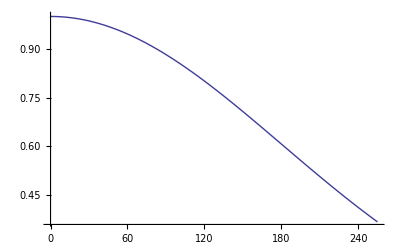

```mathematica
Plot[N[Exp[-1 x^2/255^2]],{x,0,255},PlotRange->All]
```

## Plots

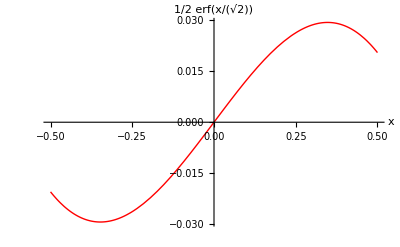

```mathematica
Plot[{Erf[x/1.0]-x},{x,-0.5,0.5},PlotStyle->Red,AxesLabel->TraditionalForm/@{x,Φ[x]}]
```

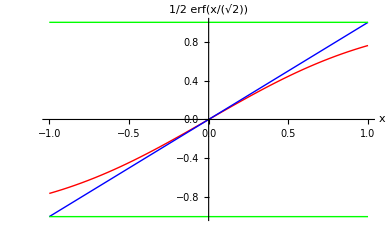

```mathematica
Plot[{Erf[x/1.2],x,1,-1},{x,-1,1},PlotStyle->{Red,Blue,Green,Green},AxesLabel->TraditionalForm/@{x,Φ[x]}]
```

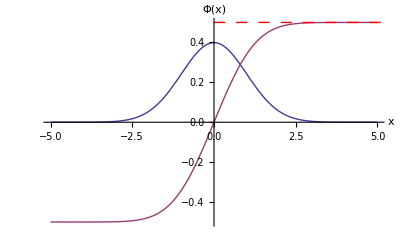

```mathematica
Plot[{PDF[NormalDistribution[0,1],x],Φ[x]},{x,-5,5},PlotRange->All,AxesLabel->TraditionalForm/@{x,HoldForm[Φ[x]]},
Epilog->{Red,Dashing[{.02,.02}],Line[{{0,.5},{10,.5}}]}]
```

2

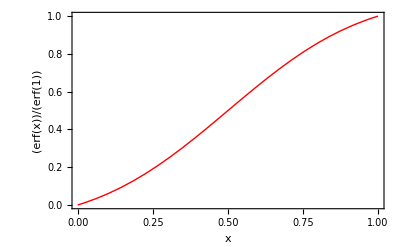

```mathematica
g=2
Plot[1/2(Erf[2 x-1]/ Erf[1]+1),{x,-1,1},PlotStyle->Red,AxesLabel->TraditionalForm/@{x,Erf[x]/Erf[1]},PlotRange->{{0,1},{0,1}},
Epilog->{Red,Dashing[{.02,.02}],Line[{{-1,1},{-1,1}}]},Frame->True]
```

## Approximations

```mathematica
Phi[1,x_]:=Which[Abs[x]≤2.2,.1 x(4.4-x),2.2<Abs[x]<2.6,.49,x≥2.6,.5]
Phi[2,x_]:=1/2 Sqrt[1-(7 Exp[-x^2/2]+16 Exp[-x^2(2-Sqrt[2])]+(7+Pi/4 x^2)Exp[-x^2])/30]
Phi[3,x_]:=1/2-1/2/(1+.196854x+.115195x^2+.000343654x^3+.019527x^4)^4
Phi[4,x_]:=1/2-(13.5806+2.7115x+.523073x^2)/(Exp[x^2/2](3.00596+x)^3)
Phi[5,x_]:=1/2-(.266784(23.1544+x)(15.2105+3.63895x+x^2))/(Exp[x^2/2](3.70247+x)^4)
```

```mathematica
Phi[2,x]//TraditionalForm
```

1/2 √(1/30 (-ⅇ^(-x^2) ((π x^2)/4+7)-7 ⅇ^(-x^2/2)-16 ⅇ^(-(2-√2) x^2))+1)

```mathematica
Phi[2,x]-Phi[2,-x]
```

0

```mathematica
FindMaximum[Abs[Phi[2,x]-Phi[x]],{x,0.001,10}]
```

{0.0000303652,{x→0.401687}}

```mathematica
Show[Block[{$DisplayFunction=Identity},
GraphicsArray[
Partition[
Table[
Plot[Phi[x]-Phi[n,x],{x,0,5},PlotStyle->Red,AxesLabel->TraditionalForm/@{x,Φ[x]-Subscript[Φ,n][x]}],{n,5}],3,3,{1,1},{}]
]
]]
```

⁃GraphicsArray⁃

```mathematica
Show[Block[{$DisplayFunction=Identity},
GraphicsArray[
Table[
Plot[Phi[x]-Phi[n,x],Evaluate[{x,Sequence@@#}],PlotStyle->Red,AxesLabel->TraditionalForm/@{x,Φ[x]-Subscript[Φ,n][x]}
]&/@{{0,5},{5,10}},{n,4}]
]
]]
```

⁃GraphicsArray⁃

## First Quartile

### 1/4

```mathematica
Solve[1/2 ( Erf[t/(√2)]+1)==1/4,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→√2 InverseErf[-1/2]}}

```mathematica
FindRoot[1/2 ( Erf[t/(√2)]+1)==1/4,{t,1}]
```

{t→-0.67449}

```mathematica
Reduce[1/2 ( Erf[t/(√2)]+1)==1/4&&-1<t<0,t,Reals]
```

Reduce::nint: Warning: Reduce used numeric integration to prove that the solution set found is complete.

t==Root[{1+2 Erf[#1/(√2)]&,-0.674489750196081743202227014541}]

```mathematica
expr1=Root[{1+2 Erf[#1/(√2)]&,-0.6744897501960817432022270145412998175939784590407714589584`30.102999566398122}];
expr2=√2 InverseErf[-1/2];
```

```mathematica
FullSimplify/@{expr1,expr2,expr1-expr2}
```

{Root[{1+2 Erf[#1/(√2)]&,-0.674489750196081743202227014541}],√2 InverseErf[-1/2],0}

```mathematica
ByteCount/@{expr1,expr2}
```

{544,272}

### 3/4

```mathematica
Solve[1/2 ( Erf[t/(√2)]+1)==3/4,t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→√2 InverseErf[1/2]}}

## Series Expansion

```mathematica
Expand[(2ser-1)Sqrt[π/2]Exp[x^2/2]]
```

945/x^11-105/x^9+15/x^7-3/x^5+1/x^3-1/x

### V4.x

```mathematica
Series[Φ[x],{x,∞,10}]
```

1/2 Erf[1/(√2 x)+O[x]^11]

### V5.2

```mathematica
Series[Φ[x],{x,∞,10}]//Simplify//TraditionalForm
```

Series::esss: Essential singularity encountered in ⅇ.

General::stop: Further output of Series :: "esss" will be suppressed during this calculation.

ⅇ^(-x^2/2) (-1/(√(2 π) x)+(1/x)^3/(√(2 π))-(3 (1/x)^5)/(√(2 π))+(15 (1/x)^7)/(√(2 π))-(105 (1/x)^9)/(√(2 π))+O((1/x)^11))+1/2

### V6

```mathematica
Series[Φ[x],{x,∞,10}]//Simplify//TraditionalForm
```

ⅇ^(-x^2/2) (-1/(√(2 π) x)+1/(√(2 π) x^3)-3/(√(2 π) x^5)+15/(√(2 π) x^7)-105/(√(2 π) x^9)+O((1/x)^11))+1/2

## Approx

```mathematica
Clear[y,a1,a2,a3,a4,a5,p]
```

```mathematica
A1[prec_:pre]:=Rationalize[a1,pre];
```

```mathematica
A1[]
```

a1

```mathematica
a1=0.254829592;
A1[prec_:pre]:=Rationalize[a1,prec];
a2=0.284496736;
A2[prec_:pre]:=Rationalize[a2,prec];
a3=1.421413741;
A3[prec_:pre]:=Rationalize[a3,prec];
a4=1.453152027;
A4[prec_:pre]:=Rationalize[a4,prec];
a5=1.061405429;
A5[prec_:pre]:=Rationalize[a5,prec];
p=0.3275911;
P[prec_:pre]:=Rationalize[p,prec];
```

```mathematica
TableForm[{{"Precision","A1","A2","A3","A4","A5","P"},Sequence@@Table[pre=10^(-prec);{pre,A1[10^(-prec)]-A1[10^(-prec-1)],A2[10^(-prec)]-A2[10^(-prec-1)],A3[10^(-prec)]-A3[10^(-prec-1)],A4[10^(-prec)]-A4[10^(-prec-1)],A5[10^(-prec)]-A5[10^(-prec-1)],P[10^(-prec)]-P[10^(-prec-1)]},{prec,1,12}]}]
```

Precision | A1 | A2 | A3 | A4 | A5 | P
1/10 | 1/12 | 1/21 | 1/14 | 1/18 | -1/16 | 0
1/100 | -1/172 | 1/469 | 1/133 | -1/126 | 1/528 | 1/156
1/1000 | 2/2193 | -6/7303 | -1/2299 | -1/1344 | -1/1254 | -1/1508
1/10000 | 1/13209 | -5/51339 | 3/36179 | -1/29376 | 0 | 0
1/100000 | -1/281533 | 1/276477 | -3/304382 | 2/269433 | -1/345306 | -1/171738
1/1000000 | 1/3826240 | 1/1446368 | 3/3413354 | -1/2029846 | 12/13318513 | 1/1145907
1/10000000 | -1/22411840 | 1/41052704 | -3/37141181 | 1/10998169 | 3/40170992 | 2/36797895
1/100000000 | -1/382975050 | -3/400747033 | 0 | -1/132385132 | 0 | 1/372268340
1/1000000000 | 1/1287480675 | 1/2254920644 | -1/1173718920 | 1/1648372836 | 0 | 0
1/10000000000 | -1/10450533080 | -1/15437951900 | 1/23628762120 | 2/28068830373 | 1/12228362416 | 1/48049183804
1/100000000000 | 1/248828830680 | -1/255740604350 | -1/123084086138 | -1/453609848270 | -19/2023870273265 | -27/3156839285029
1/1000000000000 | 0 | -3/3453454807957 | 1/4083575921646 | 3/4637475946610 | -3/4614123805970 | -5/5767134568101

{1/12,-1/172,2/2193,1/13209,-1/281533,1/3826240,-1/22411840,-1/382975050,1/1287480675,-1/10450533080,1/248828830680,0,-1/10638329485890}

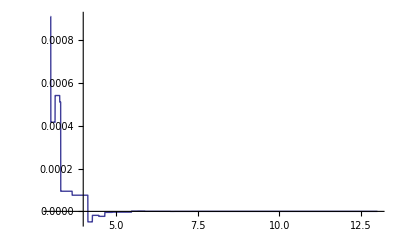

```mathematica
Table[A1[10^(-pre)]-A1[10^(-pre-1)],{pre,1,13}]
Plot[A1[10^(-pre)]-A1[10^(-pre-1)],{pre,3,13},PlotRange->All]
```

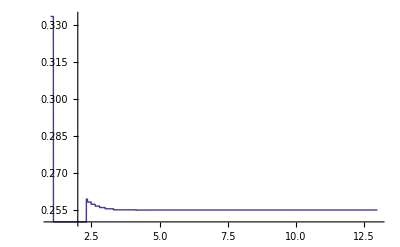

```mathematica
Plot[A1[10^(-pre)],{pre,1,13},PlotRange->All]
```

```mathematica
prec
```

0.1

```mathematica
t[x_]:=1/(1+P x)
t[a_,b_]:=b/(b+a P)
erfP[x__]:=(((((A5 t[x]-A4) t[x])+A3) t[x]-A2) t[x]+A1)
erfH[a_,b___]:=1-erfP[a,b] t[a,b] Exp[-1 a^2/b^2]
erfA[x_]:=Piecewise[{{erfH[x],x≥0},{-erfH[-x],x<0}}]
error[x_]:=erfA[x]-Erf[x];
```

```mathematica
Collect[Numerator[Together[erfP[a,b]]],b,Simplify]/ Denominator[Together[erfP[a/b]]]
InputForm[%]
```

((A1-A2+A3-A4+A5) b^4+a (4 A1-3 A2+2 A3-A4) b^3 P+a^2 (6 A1-3 A2+A3) b^2 P^2+a^3 (4 A1-A2) b P^3+a^4 A1 P^4)/(b+a P)^4

```mathematica
((A1 - A2 + A3 - A4 + A5) b^4 + a (4 A1 - 3 A2 + 2 A3 - A4) b^3 P + a^2 (6 A1 - 3 A2 + A3) b^2 P^2 + a^3 (4 A1 - A2) b P^3 + a^4 A1 P^4)/
 (b + a P)^4
```

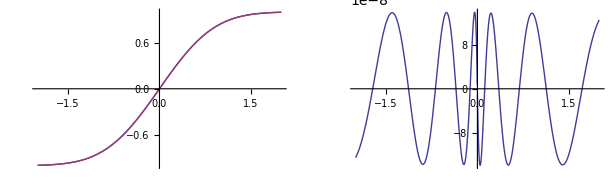

```mathematica
GraphicsRow[{Plot[{Erf[x],erfRA[x,1]},{x,-2,2}],Plot[Erf[x]-erfRA[x,1],{x,-2,2}]}]
```

```mathematica
Manipulate[
GraphicsRow[{Plot[{Floor[rErf[x, g,c,sMin,sMax,dMin,2^dMax,erfHC]]},{x,sMin,sMax},PlotStyle->{Blue},AxesLabel->TraditionalForm/@{x,Φ[x]},PlotRange->{{sMin,sMax},{dMin, 2^dMax}},Filling->Bottom,PlotPoints->2(sMax-sMin+1),
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,2^dMax-1},{sMax,2^dMax-1}}], Line[{{sMin,dMin},{sMax,dMin}}]}],
Plot[{Floor[rErf[x, g,c,sMin,sMax,dMin,2^dMax,erfHC]]-Floor[nErf[x, g,c,sMin,sMax,dMin,2^dMax,Erf]]},{x,sMin,sMax},PlotStyle->{Red},AxesLabel->TraditionalForm/@{x,Φ[x]},PlotRange->{{sMin,sMax},Automatic},Filling->Axis,PlotPoints->2(sMax-sMin+1)]}],
{dMin,0,255,1,ValueThumbSlider[##]&},{{dMax,8},1,64,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{{c,(sMax+sMin)/2},sMin,sMax,1,ValueThumbSlider[##]&},{{g,1},1,10,ValueThumbSlider[##]&}
]
```

Plot::exclul: {Sin[π\ Re[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0, Sin[π\ Im[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, Sin[π\ Im[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, Sin[π\ Re[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0, Sin[π\ Im[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {(-255/2 + x) - 0, (255/2 - x) - 0, Sin[128\ π\ Re[erfHC[« 2 »] + Piecewise[« 2 »]/erfHC[« 2 »]]] - 0, Sin[128\ π\ Im[erfHC[« 2 »] + Piecewise[« 2 »]/erfHC[« 2 »]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, Sin[π\ Im[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, (-255/2 + x) - 0, (255/2 - x) - 0, Sin[128\ π\ Re[erfHC[« 2 »] + Piecewise[« 2 »]/erfHC[« 2 »]]] - 0, Sin[128\ π\ Im[erfHC[« 2 »] + Piecewise[« 2 »]/erfHC[« 2 »]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0, Sin[π\ Im[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, Sin[π\ Im[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, Sin[π\ Re[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0, Sin[π\ Im[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0, Sin[π\ Im[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, Sin[π\ Im[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, Sin[π\ Re[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0, Sin[π\ Im[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0, Sin[π\ Im[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, Sin[π\ Im[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, Sin[π\ Re[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0, Sin[π\ Im[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0, Sin[π\ Im[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, Sin[π\ Im[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, Sin[π\ Re[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0, Sin[π\ Im[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0, Sin[π\ Im[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, Sin[π\ Im[nErf[x, 1, 255/2, 0, 255, 0, 256, Erf]]] - 0, Sin[π\ Re[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0, Sin[π\ Im[rErf[x, 1, 255/2, 0, 255, 0, 256, erfHC]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Im[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Im[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {(-25/2 + x) - 0, (25/2 - x) - 0, Sin[14\ π\ Re[erfRA[« 2 »] + Piecewise[« 2 »]/erfRA[« 2 »]]] - 0, Sin[14\ π\ Im[erfRA[« 2 »] + Piecewise[« 2 »]/erfRA[« 2 »]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Im[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, (-25/2 + x) - 0, (25/2 - x) - 0, Sin[14\ π\ Re[erfRA[« 2 »] + Piecewise[« 2 »]/erfRA[« 2 »]]] - 0, Sin[14\ π\ Im[erfRA[« 2 »] + Piecewise[« 2 »]/erfRA[« 2 »]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Im[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Im[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Im[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Im[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Im[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

Plot::exclul: {Sin[π\ Re[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Im[nErf[x, 4.72, 25/2, 0, 25, 0, 28, Erf]]] - 0, Sin[π\ Re[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0, Sin[π\ Im[rErf[x, 4.72, 25/2, 0, 25, 0, 28, erfRA]]] - 0} must be a list of equalities or real-valued functions.

```mathematica
2^64
```

18446744073709551616

```mathematica
FullSimplify[%]
```

1-(b ((3 a^4)/1022+(31 a^3 b)/1200+(178 a^2 b^2)/791+(213 a b^3)/418+b^4) ⅇ^(-a^2/b^2))/((970 a)/2961+b)^5

```mathematica
nErf[x_, g_,c_,xMin_,xMax_,yMin_,yMax_]:=yMin+((-yMax+yMin) (erfHC[(g (-c+x)),(xMax-xMin)]+erfHC[(g (c-xMin)),(xMax-xMin)]))/(erfHC[(g (c-xMax)),(xMax-xMin)]+erfHC[(g (-c+xMin)),(xMax-xMin)])
```

```mathematica
Exp[-1 (a/b)^2]
```

ⅇ^(-a^2/b^2)

```mathematica
Simplify[scaleCast[sMin, dMin, dMax,sMin,sMax,c,g]]
```

dMin

```mathematica
FullSimplify[Expand[2 g(sMin-c-(sMax +sMin)/2)/(sMax - sMin)]]
FullSimplify[g(1-2 c/(sMax-sMin))]
```

g (-1+(2 c)/(-sMax+sMin))

g+(2 c g)/(-sMax+sMin)

```mathematica
scaleCast[x_,dMin_,dMax_,sMin_,sMax_,c_,g_]:= ((dMax - dMin)/2)( Erf[2 g(x-c-(sMax +sMin)/2)/(sMax - sMin)]/Erf[g(1+2 c/(sMax-sMin))]+1)+dMin
```

```mathematica
scaleCast[x_,dMin_,dMax_,sMin_,sMax_,c_,g_]:= Floor[((dMax - dMin)/2)( erfA[2 g(x-c-(sMax +sMin)/2)/(sMax - sMin)]/erfA[g]+1)+dMin]
```

```mathematica
tx[x_]:=1/(1+pp x)
Collect[Simplify[Together[Expand[tx[2 g(x-c-(sMax +sMin)/2)/(sMax  -sMin)]]]],g]
```

(-sMax+sMin)/(2 c g pp+(-1+g pp) sMax+sMin+g pp sMin-2 g pp x)

```mathematica
Denominator[1./(1.-(0.3275911 g (2. c+sMax+sMin-2. x))/(sMax-1. sMin))]
```

1.-(0.327591 g (2. c+sMax+sMin-2. x))/(sMax-1. sMin)

```mathematica
Manipulate[
Plot[{scaleCast[x, dMin, dMax,sMin,sMax,c,g]},{x,sMin,sMax},PlotStyle->{Blue},AxesLabel->TraditionalForm/@{x,Φ[x]},PlotRange->{{sMin,sMax},{dMin, dMax}},Filling->Bottom,PlotPoints->sMax-sMin+1,
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,dMax},{sMax,dMax}}], Line[{{sMin,dMin},{sMax,dMin}}]}],
{dMin,0,255,1,ValueThumbSlider[##]&},{{dMax,255},1,255,1,ValueThumbSlider[##]&},{sMin,0,sMax,1,ValueThumbSlider[##]&},{{sMax,255},1,255,1,ValueThumbSlider[##]&},{c,sMin,sMax,1,ValueThumbSlider[##]&},{{g,1},0,4,ValueThumbSlider[##]&}
]
```

```mathematica
Manipulate[
Plot[{scaleCast[x, dMin, dMax,sMin,sMax,c,g]},{x,sMin,sMax},PlotStyle->{Red,Blue,Green,Green},AxesLabel->TraditionalForm/@{x,Φ[x]},
Epilog->{Red,Dashing[{.02,.02}],Line[{{sMin,dMax},{sMax,dMax}}], Line[{{sMin,dMin},{sMax,dMin}}]}],
{dMin,0,255,ValueThumbSlider[##]&},{dMax,1,255,ValueThumbSlider[##]&},{sMin,0,255,ValueThumbSlider[##]&},{sMax,1,255,ValueThumbSlider[##]&},{c,sMin,sMax,ValueThumbSlider[##]&},{{g,1},0,2,ValueThumbSlider[##]&}
]
```

```mathematica
Erf[2]
```

Erf[2]

```mathematica
N[Erf[2]]
```

0.995322

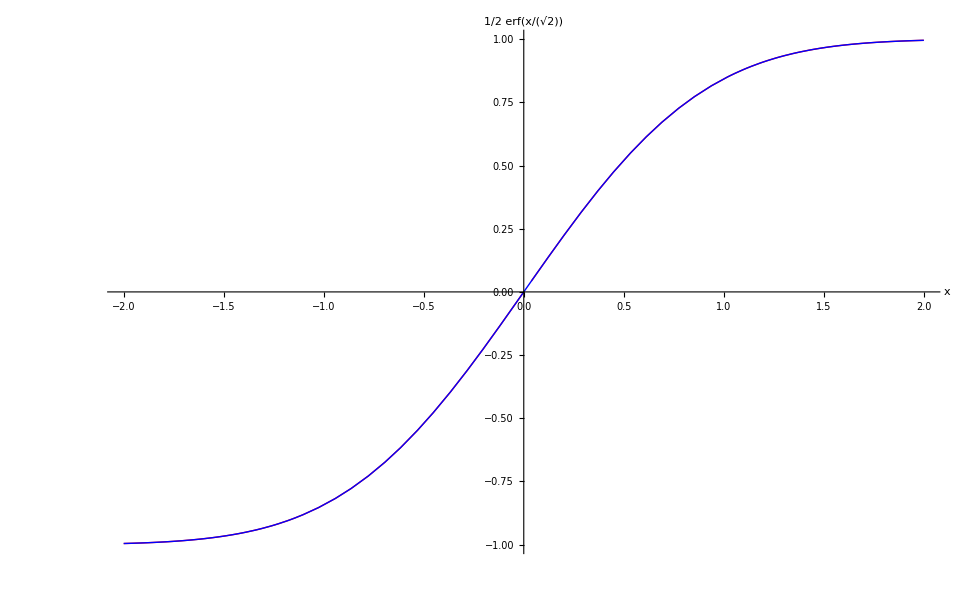

```mathematica
Plot[{erfA[x],Erf[x]},{x,-2,2},PlotStyle->{Red,Blue,Green,Green},AxesLabel->TraditionalForm/@{x,Φ[x]}]
```

```mathematica
1.0-(((((a5 t[x]+a4) t[x])+a3) t[x]+a2) t[x]+a1) t[x] Exp[-1 x^2]
```

```mathematica
Expand[yp[x]]
   FullSimplify[%]
```

1.-(1.06141 ⅇ^(-x^2))/(1.+0.327591 x)^5+(1.45315 ⅇ^(-x^2))/(1.+0.327591 x)^4-(1.42141 ⅇ^(-x^2))/(1.+0.327591 x)^3+(0.284497 ⅇ^(-x^2))/(1.+0.327591 x)^2-(0.25483 ⅇ^(-x^2))/(1.+0.327591 x)

1/(3.05259+1. x)^5 ⅇ^(-x^2) (-265.057+x (-135.065+x (-59.646+(-6.84727-0.777889 x) x))+ⅇ^(x^2) (265.057+x (434.152+x (284.449+x (93.1828+x (15.2629+1. x))))))

```mathematica
p1[x_]:=(1.06141 )/(1.+0.327591 x)^5
p2[x_]:=(1.45315 )/(1.+0.327591 x)^4
p3[x_]:=-(1.42141 )/(1.+0.327591 x)^3
p4[x_]:=(0.284497 )/(1.+0.327591 x)^2
p5[x_]:=(0.25483 )/(1.+0.327591 x)
```

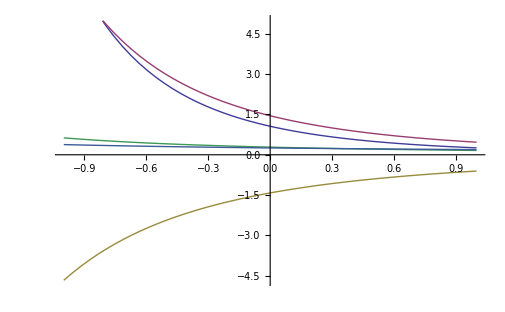

```mathematica
Plot[{p1[x],p2[x],p3[x],p4[x],p5[x]},{x,-1,1}]
```

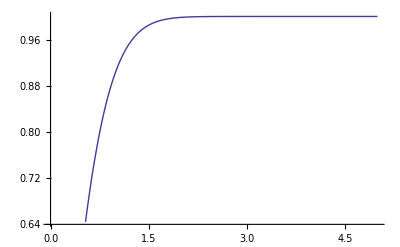

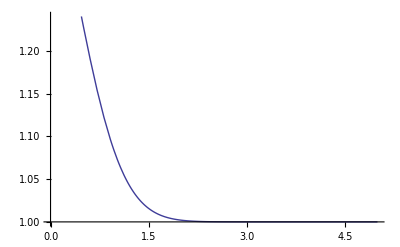

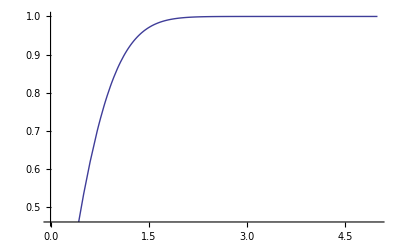

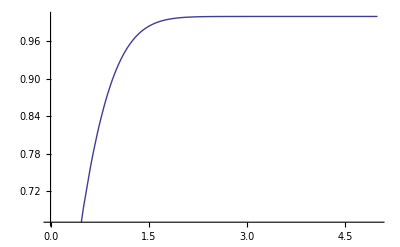

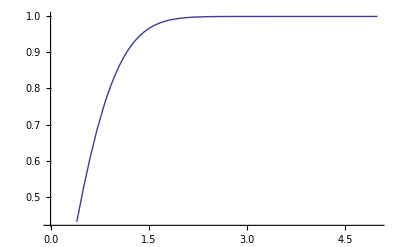

```mathematica
Plot[1.-(1.06141 E^-x^2)/(1.+0.327591 x)^5,{x,0,5}]

Plot[1.-(1.06141 E^-x^2)/(1.+0.327591 x)^5+(1.45315 E^-x^2)/(1.+0.327591 x)^4,{x,0,5}]

Plot[1.-(1.06141 E^-x^2)/(1.+0.327591 x)^5+(1.45315 E^-x^2)/(1.+0.327591 x)^4-(1.42141 E^-x^2)/(1.+0.327591 x)^3,{x,0,5}]

Plot[1.-(1.06141 E^-x^2)/(1.+0.327591 x)^5+(1.45315 E^-x^2)/(1.+0.327591 x)^4-(1.42141 E^-x^2)/(1.+0.327591 x)^3+(0.284497 E^-x^2)/(1.+0.327591 x)^2,{x,0,5}]

Plot[1.-(1.06141 E^-x^2)/(1.+0.327591 x)^5+(1.45315 E^-x^2)/(1.+0.327591 x)^4-(1.42141 E^-x^2)/(1.+0.327591 x)^3+(0.284497 E^-x^2)/(1.+0.327591 x)^2-(0.25483 E^-x^2)/(1.+0.327591 x),{x,0,5}]
```

```mathematica
erfI=InverseFunction[(1. - 
  (1. (0.254829592 + 
     (1. (-0.284496736 + (1. (1.421413741 + 
           (1. (-1.453152027 + 1.061405429/(1. + 0.3275911 #)))/
            (1. + 0.3275911 #)))/(1. + 0.3275911 #)))/(1. + 0.3275911 #)))/
   (E^#^2 (1. + 0.3275911 #)))&]
```

InverseFunction[1.-(1. (0.25483+(1. (-0.284497+(1. (1.42141+(1. (-1.45315+1.06141/(1.+0.327591 #1)))/(1.+0.327591 #1)))/(1.+0.327591 #1)))/(1.+0.327591 #1)))/(ⅇ^(#1^2) (1.+0.327591 #1))&]

```mathematica
InverseFunction[y]
```

y^(-1)

```mathematica
y[1]
```

0.842701

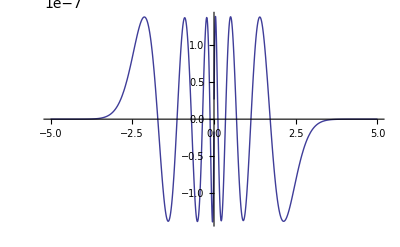

```mathematica
Plot[error[x],{x,-5,5}]
```

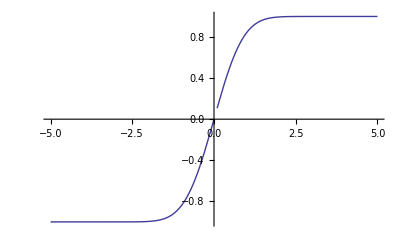

```mathematica
Plot[y[x],{x,-5,5}]
```

```mathematica
#include<cmath>double erf(double x)
{
//constants double a1=0.254829592;
double a2=-0.284496736;
double a3=1.421413741;
double a4=-1.453152027;
double a5=1.061405429;
double p=0.3275911;//Save the sign of x int sign=1;
if (x<0) sign=-1;
x=fabs(x);//A&S formula 7.1.26 double t=1.0/(1.0+p x);
double y=1.0-(((((a5 t+a4) t)+a3) t+a2) t+a1) t exp(-x x);
return sign y;}

void testErf()
{
//Select a few input values double x[]={-3,-1,0.0,0.5,2.1};//Output computed by Mathematica//y=Erf[x] double y[]={-0.999977909503,-0.842700792950,0.0,0.520499877813,0.997020533344};
int numTests=sizeof(x)/sizeof(double);
double maxError=0.0;
for (int i=0;i<numTests;++i) {double error=fabs(y[i]-erf(x[i]));
if (error>maxError) maxError=error;} std::cout <<"Maximum error: " <<maxError <<"\n";}
```